```mathematica
x/.NSolve[x^4==x+1,x][[4]]
```

1.22074

```mathematica
ph3=1.2207440846057596
```

1.22074

```mathematica
init={0,0,0};
n=33^2;
RGBColor/@(init+(#-Floor[#]&/@({ph3^-1,ph3^-2,ph3^-3}#))&/@Range[0,n]);
```

```mathematica
?Floor
```

Floor[x] gives the greatest integer less than or equal to x. 
Floor[x,a] gives the greatest multiple of a less than or equal to x.

```mathematica
Partition[%845,33]//MatrixForm
```

(RGBColor[{0., 0., 0.}] | RGBColor[{0.8191725133961644, 0.671043606703789, 0.5497004779019701}] | RGBColor[{0.6383450267923287, 0.3420872134075781, 0.09940095580394015}] | RGBColor[{0.4575175401884932, 0.013130820111367125, 0.6491014337059102}] | RGBColor[{0.2766900535846575, 0.6841744268151562, 0.1988019116078803}] | RGBColor[{0.09586256698082174, 0.3552180335189452, 0.7485023895098504}] | RGBColor[{0.9150350803769864, 0.02626164022273425, 0.29820286741182045}] | RGBColor[{0.7342075937731503, 0.6973052469265237, 0.8479033453137905}] | RGBColor[{0.553380107169315, 0.36834885363031233, 0.3976038232157606}] | RGBColor[{0.37255262056547966, 0.03939246033410093, 0.9473043011177307}] | RGBColor[{0.19172513396164348, 0.7104360670378904, 0.49700477901970075}] | RGBColor[{0.010897647357808182, 0.3814796737416799, 0.046705256921670824}] | RGBColor[{0.8300701607539729, 0.0525232804454685, 0.5964057348236409}] | RGBColor[{0.6492426741501376, 0.7235668871492571, 0.14610621272561097}] | RGBColor[{0.4684151875463005, 0.3946104938530475, 0.695806690627581}] | RGBColor[{0.2875877009424652, 0.06565410055683607, 0.24550716852955112}] | RGBColor[{0.10676021433862992, 0.7366977072606247, 0.7952076464315212}] | RGBColor[{0.9259327277347946, 0.40774131396441327, 0.3449081243334913}] | RGBColor[{0.7451052411309593, 0.07878492066820186, 0.8946086022354613}] | RGBColor[{0.5642777545271223, 0.7498285273719922, 0.4443090801374314}] | RGBColor[{0.38345026792328696, 0.42087213407578083, 0.9940095580394015}] | RGBColor[{0.20262278131945166, 0.09191574077956943, 0.5437100359413716}] | RGBColor[{0.021795294715616365, 0.7629593474833598, 0.09341051384334165}] | RGBColor[{0.8409678081117811, 0.4340029541871484, 0.6431109917453117}] | RGBColor[{0.6601403215079458, 0.105046560890937, 0.1928114696472818}] | RGBColor[{0.4793128349041105, 0.7760901675947274, 0.7425119475492519}] | RGBColor[{0.2984853483002752, 0.4471337742985142, 0.29221242545122195}] | RGBColor[{0.11765786169643633, 0.11817738100230457, 0.841912903353192}] | RGBColor[{0.936830375092601, 0.789220987706095, 0.3916133812551621}] | RGBColor[{0.7560028884887657, 0.46026459440988177, 0.9413138591571322}] | RGBColor[{0.5751754018849304, 0.13130820111367214, 0.49101433705910225}] | RGBColor[{0.39434791528109514, 0.802351807817459, 0.040714814961070545}] | RGBColor[{0.21352042867725984, 0.47339541452124934, 0.5904152928630424}]
RGBColor[{0.03269294207342455, 0.1444390212250397, 0.14011577076501425}] | RGBColor[{0.8518654554695893, 0.8154826279288265, 0.6898162486669825}] | RGBColor[{0.671037968865754, 0.4865262346326169, 0.23951672656895084}] | RGBColor[{0.49021048226191866, 0.15756984133640373, 0.7892172044709227}] | RGBColor[{0.30938299565808336, 0.8286134480401941, 0.33891768237289455}] | RGBColor[{0.1285555090542445, 0.4996570547439845, 0.8886181602748628}] | RGBColor[{0.9477280224504092, 0.1707006614477713, 0.43831863817683114}] | RGBColor[{0.7669005358465739, 0.8417442681515617, 0.988019116078803}] | RGBColor[{0.5860730492427422, 0.512787874855352, 0.5377195939807748}] | RGBColor[{0.4052455626389033, 0.18383148155913887, 0.08742007188274314}] | RGBColor[{0.22441807603506447, 0.8548750882629292, 0.6371205497847114}] | RGBColor[{0.04359058943123273, 0.5259186949667196, 0.1868210276866833}] | RGBColor[{0.8627631028273939, 0.19696230167050643, 0.7365215055886551}] | RGBColor[{0.6819356162235621, 0.8680059083742968, 0.28622198349062344}] | RGBColor[{0.5011081296197233, 0.5390495150780836, 0.8359224613925917}] | RGBColor[{0.32028064301589154, 0.210093121781874, 0.3856229392945636}] | RGBColor[{0.1394531564120527, 0.8811367284856644, 0.9353234171965354}] | RGBColor[{0.958625669808221, 0.5521803351894548, 0.48502389509850374}] | RGBColor[{0.7777981832043821, 0.22322394189323802, 0.03472437300047204}] | RGBColor[{0.5969706966005504, 0.8942675485970284, 0.5844248509024439}] | RGBColor[{0.4161432099967115, 0.5653111553008188, 0.13412532880441574}] | RGBColor[{0.23531572339287266, 0.23635476200460914, 0.683825806706384}] | RGBColor[{0.05448823678904091, 0.9073983687083995, 0.23352628460835234}] | RGBColor[{0.8736607501852021, 0.5784419754121899, 0.7832267625103242}] | RGBColor[{0.6928332635813703, 0.24948558211597316, 0.33292724041229604}] | RGBColor[{0.5120057769775315, 0.9205291888197635, 0.8826277183142643}] | RGBColor[{0.3311782903736997, 0.5915727955235539, 0.43232819621623264}] | RGBColor[{0.15035080376986087, 0.2626164022273443, 0.9820286741182045}] | RGBColor[{0.9695233171660291, 0.9336600089311347, 0.5317291520201763}] | RGBColor[{0.7886958305621903, 0.6047036156349179, 0.08142962992214109}] | RGBColor[{0.6078683439583585, 0.2757472223387083, 0.6311301078241129}] | RGBColor[{0.4270408573545197, 0.9467908290424987, 0.1808305857260848}] | RGBColor[{0.24621337075068084, 0.617834435746289, 0.7305310636280566}]
RGBColor[{0.0653858841468491, 0.2888780424500794, 0.2802315415300285}] | RGBColor[{0.8845583975430102, 0.9599216491538627, 0.8299320194319932}] | RGBColor[{0.7037309109391785, 0.6309652558576531, 0.3796324973339651}] | RGBColor[{0.5229034243353397, 0.30200886256144344, 0.9293329752359369}] | RGBColor[{0.3420759377315079, 0.9730524692652338, 0.4790334531379017}] | RGBColor[{0.16124845112766906, 0.6440960759690242, 0.02873393103987354}] | RGBColor[{0.9804209645238373, 0.31513968267280745, 0.5784344089418454}] | RGBColor[{0.7995934779199985, 0.9861832893765978, 0.12813488684381724}] | RGBColor[{0.6187659913161667, 0.6572268960803882, 0.6778353647457891}] | RGBColor[{0.43793850471232787, 0.3282705027841786, 0.22753584264775384}] | RGBColor[{0.257111018108489, 0.999314109487969, 0.7772363205497257}] | RGBColor[{0.07628353150465728, 0.6703577161917593, 0.32693679845169754}] | RGBColor[{0.8954560449008184, 0.3414013228955426, 0.8766372763536623}] | RGBColor[{0.7146285582969796, 0.012444929599332966, 0.42633775425563414}] | RGBColor[{0.5338010716931478, 0.6834885363031233, 0.976038232157606}] | RGBColor[{0.3529735850893161, 0.3545321430069137, 0.5257387100595778}] | RGBColor[{0.17214609848548434, 0.025575749710704088, 0.07543918796154969}] | RGBColor[{0.9913186118816384, 0.6966193564144874, 0.6251396658635144}] | RGBColor[{0.8104911252778066, 0.36766296311827773, 0.1748401437654863}] | RGBColor[{0.6296636386739749, 0.038706569822068104, 0.7245406216674581}] | RGBColor[{0.44883615207012895, 0.7097501765258585, 0.2742410995694229}] | RGBColor[{0.2680086654662972, 0.38079378322964885, 0.8239415774713947}] | RGBColor[{0.08718117886246546, 0.051837389933439226, 0.3736420553733666}] | RGBColor[{0.9063536922586337, 0.7228809966372225, 0.9233425332753384}] | RGBColor[{0.7255262056547878, 0.39392460334101287, 0.4730430111773103}] | RGBColor[{0.544698719050956, 0.06496821004480324, 0.022743489079275037}] | RGBColor[{0.36387123244712427, 0.7360118167485936, 0.5724439669812469}] | RGBColor[{0.18304374584329253, 0.407055423452384, 0.12214444488321874}] | RGBColor[{0.002216259239446572, 0.07809903015616726, 0.6718449227851835}] | RGBColor[{0.8213887726356148, 0.7491426368599576, 0.22154540068715534}] | RGBColor[{0.6405612860317831, 0.420186243563748, 0.7712458785891272}] | RGBColor[{0.45973379942793713, 0.09122985026753838, 0.32094635649109904}] | RGBColor[{0.2789063128241054, 0.7622734569713288, 0.8706468343930709}])

```mathematica
Partition[%845,10]//MatrixForm
```

(RGBColor[{0., 0., 0.}] | RGBColor[{0.8191725133961644, 0.671043606703789, 0.5497004779019701}] | RGBColor[{0.6383450267923287, 0.3420872134075781, 0.09940095580394015}] | RGBColor[{0.4575175401884932, 0.013130820111367125, 0.6491014337059102}] | RGBColor[{0.2766900535846575, 0.6841744268151562, 0.1988019116078803}] | RGBColor[{0.09586256698082174, 0.3552180335189452, 0.7485023895098504}] | RGBColor[{0.9150350803769864, 0.02626164022273425, 0.29820286741182045}] | RGBColor[{0.7342075937731503, 0.6973052469265237, 0.8479033453137905}] | RGBColor[{0.553380107169315, 0.36834885363031233, 0.3976038232157606}] | RGBColor[{0.37255262056547966, 0.03939246033410093, 0.9473043011177307}]
RGBColor[{0.19172513396164348, 0.7104360670378904, 0.49700477901970075}] | RGBColor[{0.010897647357808182, 0.3814796737416799, 0.046705256921670824}] | RGBColor[{0.8300701607539729, 0.0525232804454685, 0.5964057348236409}] | RGBColor[{0.6492426741501376, 0.7235668871492571, 0.14610621272561097}] | RGBColor[{0.4684151875463005, 0.3946104938530475, 0.695806690627581}] | RGBColor[{0.2875877009424652, 0.06565410055683607, 0.24550716852955112}] | RGBColor[{0.10676021433862992, 0.7366977072606247, 0.7952076464315212}] | RGBColor[{0.9259327277347946, 0.40774131396441327, 0.3449081243334913}] | RGBColor[{0.7451052411309593, 0.07878492066820186, 0.8946086022354613}] | RGBColor[{0.5642777545271223, 0.7498285273719922, 0.4443090801374314}]
RGBColor[{0.38345026792328696, 0.42087213407578083, 0.9940095580394015}] | RGBColor[{0.20262278131945166, 0.09191574077956943, 0.5437100359413716}] | RGBColor[{0.021795294715616365, 0.7629593474833598, 0.09341051384334165}] | RGBColor[{0.8409678081117811, 0.4340029541871484, 0.6431109917453117}] | RGBColor[{0.6601403215079458, 0.105046560890937, 0.1928114696472818}] | RGBColor[{0.4793128349041105, 0.7760901675947274, 0.7425119475492519}] | RGBColor[{0.2984853483002752, 0.4471337742985142, 0.29221242545122195}] | RGBColor[{0.11765786169643633, 0.11817738100230457, 0.841912903353192}] | RGBColor[{0.936830375092601, 0.789220987706095, 0.3916133812551621}] | RGBColor[{0.7560028884887657, 0.46026459440988177, 0.9413138591571322}]
RGBColor[{0.5751754018849304, 0.13130820111367214, 0.49101433705910225}] | RGBColor[{0.39434791528109514, 0.802351807817459, 0.040714814961070545}] | RGBColor[{0.21352042867725984, 0.47339541452124934, 0.5904152928630424}] | RGBColor[{0.03269294207342455, 0.1444390212250397, 0.14011577076501425}] | RGBColor[{0.8518654554695893, 0.8154826279288265, 0.6898162486669825}] | RGBColor[{0.671037968865754, 0.4865262346326169, 0.23951672656895084}] | RGBColor[{0.49021048226191866, 0.15756984133640373, 0.7892172044709227}] | RGBColor[{0.30938299565808336, 0.8286134480401941, 0.33891768237289455}] | RGBColor[{0.1285555090542445, 0.4996570547439845, 0.8886181602748628}] | RGBColor[{0.9477280224504092, 0.1707006614477713, 0.43831863817683114}]
RGBColor[{0.7669005358465739, 0.8417442681515617, 0.988019116078803}] | RGBColor[{0.5860730492427422, 0.512787874855352, 0.5377195939807748}] | RGBColor[{0.4052455626389033, 0.18383148155913887, 0.08742007188274314}] | RGBColor[{0.22441807603506447, 0.8548750882629292, 0.6371205497847114}] | RGBColor[{0.04359058943123273, 0.5259186949667196, 0.1868210276866833}] | RGBColor[{0.8627631028273939, 0.19696230167050643, 0.7365215055886551}] | RGBColor[{0.6819356162235621, 0.8680059083742968, 0.28622198349062344}] | RGBColor[{0.5011081296197233, 0.5390495150780836, 0.8359224613925917}] | RGBColor[{0.32028064301589154, 0.210093121781874, 0.3856229392945636}] | RGBColor[{0.1394531564120527, 0.8811367284856644, 0.9353234171965354}]
RGBColor[{0.958625669808221, 0.5521803351894548, 0.48502389509850374}] | RGBColor[{0.7777981832043821, 0.22322394189323802, 0.03472437300047204}] | RGBColor[{0.5969706966005504, 0.8942675485970284, 0.5844248509024439}] | RGBColor[{0.4161432099967115, 0.5653111553008188, 0.13412532880441574}] | RGBColor[{0.23531572339287266, 0.23635476200460914, 0.683825806706384}] | RGBColor[{0.05448823678904091, 0.9073983687083995, 0.23352628460835234}] | RGBColor[{0.8736607501852021, 0.5784419754121899, 0.7832267625103242}] | RGBColor[{0.6928332635813703, 0.24948558211597316, 0.33292724041229604}] | RGBColor[{0.5120057769775315, 0.9205291888197635, 0.8826277183142643}] | RGBColor[{0.3311782903736997, 0.5915727955235539, 0.43232819621623264}]
RGBColor[{0.15035080376986087, 0.2626164022273443, 0.9820286741182045}] | RGBColor[{0.9695233171660291, 0.9336600089311347, 0.5317291520201763}] | RGBColor[{0.7886958305621903, 0.6047036156349179, 0.08142962992214109}] | RGBColor[{0.6078683439583585, 0.2757472223387083, 0.6311301078241129}] | RGBColor[{0.4270408573545197, 0.9467908290424987, 0.1808305857260848}] | RGBColor[{0.24621337075068084, 0.617834435746289, 0.7305310636280566}] | RGBColor[{0.0653858841468491, 0.2888780424500794, 0.2802315415300285}] | RGBColor[{0.8845583975430102, 0.9599216491538627, 0.8299320194319932}] | RGBColor[{0.7037309109391785, 0.6309652558576531, 0.3796324973339651}] | RGBColor[{0.5229034243353397, 0.30200886256144344, 0.9293329752359369}]
RGBColor[{0.3420759377315079, 0.9730524692652338, 0.4790334531379017}] | RGBColor[{0.16124845112766906, 0.6440960759690242, 0.02873393103987354}] | RGBColor[{0.9804209645238373, 0.31513968267280745, 0.5784344089418454}] | RGBColor[{0.7995934779199985, 0.9861832893765978, 0.12813488684381724}] | RGBColor[{0.6187659913161667, 0.6572268960803882, 0.6778353647457891}] | RGBColor[{0.43793850471232787, 0.3282705027841786, 0.22753584264775384}] | RGBColor[{0.257111018108489, 0.999314109487969, 0.7772363205497257}] | RGBColor[{0.07628353150465728, 0.6703577161917593, 0.32693679845169754}] | RGBColor[{0.8954560449008184, 0.3414013228955426, 0.8766372763536623}] | RGBColor[{0.7146285582969796, 0.012444929599332966, 0.42633775425563414}]
RGBColor[{0.5338010716931478, 0.6834885363031233, 0.976038232157606}] | RGBColor[{0.3529735850893161, 0.3545321430069137, 0.5257387100595778}] | RGBColor[{0.17214609848548434, 0.025575749710704088, 0.07543918796154969}] | RGBColor[{0.9913186118816384, 0.6966193564144874, 0.6251396658635144}] | RGBColor[{0.8104911252778066, 0.36766296311827773, 0.1748401437654863}] | RGBColor[{0.6296636386739749, 0.038706569822068104, 0.7245406216674581}] | RGBColor[{0.44883615207012895, 0.7097501765258585, 0.2742410995694229}] | RGBColor[{0.2680086654662972, 0.38079378322964885, 0.8239415774713947}] | RGBColor[{0.08718117886246546, 0.051837389933439226, 0.3736420553733666}] | RGBColor[{0.9063536922586337, 0.7228809966372225, 0.9233425332753384}]
RGBColor[{0.7255262056547878, 0.39392460334101287, 0.4730430111773103}] | RGBColor[{0.544698719050956, 0.06496821004480324, 0.022743489079275037}] | RGBColor[{0.36387123244712427, 0.7360118167485936, 0.5724439669812469}] | RGBColor[{0.18304374584329253, 0.407055423452384, 0.12214444488321874}] | RGBColor[{0.002216259239446572, 0.07809903015616726, 0.6718449227851835}] | RGBColor[{0.8213887726356148, 0.7491426368599576, 0.22154540068715534}] | RGBColor[{0.6405612860317831, 0.420186243563748, 0.7712458785891272}] | RGBColor[{0.45973379942793713, 0.09122985026753838, 0.32094635649109904}] | RGBColor[{0.2789063128241054, 0.7622734569713288, 0.8706468343930709}] | RGBColor[{0.09807882622027364, 0.43331706367511913, 0.42034731229503564}])

```mathematica
Partition[%883,33]//MatrixForm
```

(RGBColor[{0., 0., 0.}] | RGBColor[{0.8191725133961644, 0.671043606703789, 0.5497004779019701}] | RGBColor[{0.6383450267923287, 0.3420872134075781, 0.09940095580394015}] | RGBColor[{0.4575175401884932, 0.013130820111367125, 0.6491014337059102}] | RGBColor[{0.2766900535846575, 0.6841744268151562, 0.1988019116078803}] | RGBColor[{0.09586256698082174, 0.3552180335189452, 0.7485023895098504}] | RGBColor[{0.9150350803769864, 0.02626164022273425, 0.29820286741182045}] | RGBColor[{0.7342075937731503, 0.6973052469265237, 0.8479033453137905}] | RGBColor[{0.553380107169315, 0.36834885363031233, 0.3976038232157606}] | RGBColor[{0.37255262056547966, 0.03939246033410093, 0.9473043011177307}] | RGBColor[{0.19172513396164348, 0.7104360670378904, 0.49700477901970075}] | RGBColor[{0.010897647357808182, 0.3814796737416799, 0.046705256921670824}] | RGBColor[{0.8300701607539729, 0.0525232804454685, 0.5964057348236409}] | RGBColor[{0.6492426741501376, 0.7235668871492571, 0.14610621272561097}] | RGBColor[{0.4684151875463005, 0.3946104938530475, 0.695806690627581}] | RGBColor[{0.2875877009424652, 0.06565410055683607, 0.24550716852955112}] | RGBColor[{0.10676021433862992, 0.7366977072606247, 0.7952076464315212}] | RGBColor[{0.9259327277347946, 0.40774131396441327, 0.3449081243334913}] | RGBColor[{0.7451052411309593, 0.07878492066820186, 0.8946086022354613}] | RGBColor[{0.5642777545271223, 0.7498285273719922, 0.4443090801374314}] | RGBColor[{0.38345026792328696, 0.42087213407578083, 0.9940095580394015}] | RGBColor[{0.20262278131945166, 0.09191574077956943, 0.5437100359413716}] | RGBColor[{0.021795294715616365, 0.7629593474833598, 0.09341051384334165}] | RGBColor[{0.8409678081117811, 0.4340029541871484, 0.6431109917453117}] | RGBColor[{0.6601403215079458, 0.105046560890937, 0.1928114696472818}] | RGBColor[{0.4793128349041105, 0.7760901675947274, 0.7425119475492519}] | RGBColor[{0.2984853483002752, 0.4471337742985142, 0.29221242545122195}] | RGBColor[{0.11765786169643633, 0.11817738100230457, 0.841912903353192}] | RGBColor[{0.936830375092601, 0.789220987706095, 0.3916133812551621}] | RGBColor[{0.7560028884887657, 0.46026459440988177, 0.9413138591571322}] | RGBColor[{0.5751754018849304, 0.13130820111367214, 0.49101433705910225}] | RGBColor[{0.39434791528109514, 0.802351807817459, 0.040714814961070545}] | RGBColor[{0.21352042867725984, 0.47339541452124934, 0.5904152928630424}]
RGBColor[{0.03269294207342455, 0.1444390212250397, 0.14011577076501425}] | RGBColor[{0.8518654554695893, 0.8154826279288265, 0.6898162486669825}] | RGBColor[{0.671037968865754, 0.4865262346326169, 0.23951672656895084}] | RGBColor[{0.49021048226191866, 0.15756984133640373, 0.7892172044709227}] | RGBColor[{0.30938299565808336, 0.8286134480401941, 0.33891768237289455}] | RGBColor[{0.1285555090542445, 0.4996570547439845, 0.8886181602748628}] | RGBColor[{0.9477280224504092, 0.1707006614477713, 0.43831863817683114}] | RGBColor[{0.7669005358465739, 0.8417442681515617, 0.988019116078803}] | RGBColor[{0.5860730492427422, 0.512787874855352, 0.5377195939807748}] | RGBColor[{0.4052455626389033, 0.18383148155913887, 0.08742007188274314}] | RGBColor[{0.22441807603506447, 0.8548750882629292, 0.6371205497847114}] | RGBColor[{0.04359058943123273, 0.5259186949667196, 0.1868210276866833}] | RGBColor[{0.8627631028273939, 0.19696230167050643, 0.7365215055886551}] | RGBColor[{0.6819356162235621, 0.8680059083742968, 0.28622198349062344}] | RGBColor[{0.5011081296197233, 0.5390495150780836, 0.8359224613925917}] | RGBColor[{0.32028064301589154, 0.210093121781874, 0.3856229392945636}] | RGBColor[{0.1394531564120527, 0.8811367284856644, 0.9353234171965354}] | RGBColor[{0.958625669808221, 0.5521803351894548, 0.48502389509850374}] | RGBColor[{0.7777981832043821, 0.22322394189323802, 0.03472437300047204}] | RGBColor[{0.5969706966005504, 0.8942675485970284, 0.5844248509024439}] | RGBColor[{0.4161432099967115, 0.5653111553008188, 0.13412532880441574}] | RGBColor[{0.23531572339287266, 0.23635476200460914, 0.683825806706384}] | RGBColor[{0.05448823678904091, 0.9073983687083995, 0.23352628460835234}] | RGBColor[{0.8736607501852021, 0.5784419754121899, 0.7832267625103242}] | RGBColor[{0.6928332635813703, 0.24948558211597316, 0.33292724041229604}] | RGBColor[{0.5120057769775315, 0.9205291888197635, 0.8826277183142643}] | RGBColor[{0.3311782903736997, 0.5915727955235539, 0.43232819621623264}] | RGBColor[{0.15035080376986087, 0.2626164022273443, 0.9820286741182045}] | RGBColor[{0.9695233171660291, 0.9336600089311347, 0.5317291520201763}] | RGBColor[{0.7886958305621903, 0.6047036156349179, 0.08142962992214109}] | RGBColor[{0.6078683439583585, 0.2757472223387083, 0.6311301078241129}] | RGBColor[{0.4270408573545197, 0.9467908290424987, 0.1808305857260848}] | RGBColor[{0.24621337075068084, 0.617834435746289, 0.7305310636280566}]
RGBColor[{0.0653858841468491, 0.2888780424500794, 0.2802315415300285}] | RGBColor[{0.8845583975430102, 0.9599216491538627, 0.8299320194319932}] | RGBColor[{0.7037309109391785, 0.6309652558576531, 0.3796324973339651}] | RGBColor[{0.5229034243353397, 0.30200886256144344, 0.9293329752359369}] | RGBColor[{0.3420759377315079, 0.9730524692652338, 0.4790334531379017}] | RGBColor[{0.16124845112766906, 0.6440960759690242, 0.02873393103987354}] | RGBColor[{0.9804209645238373, 0.31513968267280745, 0.5784344089418454}] | RGBColor[{0.7995934779199985, 0.9861832893765978, 0.12813488684381724}] | RGBColor[{0.6187659913161667, 0.6572268960803882, 0.6778353647457891}] | RGBColor[{0.43793850471232787, 0.3282705027841786, 0.22753584264775384}] | RGBColor[{0.257111018108489, 0.999314109487969, 0.7772363205497257}] | RGBColor[{0.07628353150465728, 0.6703577161917593, 0.32693679845169754}] | RGBColor[{0.8954560449008184, 0.3414013228955426, 0.8766372763536623}] | RGBColor[{0.7146285582969796, 0.012444929599332966, 0.42633775425563414}] | RGBColor[{0.5338010716931478, 0.6834885363031233, 0.976038232157606}] | RGBColor[{0.3529735850893161, 0.3545321430069137, 0.5257387100595778}] | RGBColor[{0.17214609848548434, 0.025575749710704088, 0.07543918796154969}] | RGBColor[{0.9913186118816384, 0.6966193564144874, 0.6251396658635144}] | RGBColor[{0.8104911252778066, 0.36766296311827773, 0.1748401437654863}] | RGBColor[{0.6296636386739749, 0.038706569822068104, 0.7245406216674581}] | RGBColor[{0.44883615207012895, 0.7097501765258585, 0.2742410995694229}] | RGBColor[{0.2680086654662972, 0.38079378322964885, 0.8239415774713947}] | RGBColor[{0.08718117886246546, 0.051837389933439226, 0.3736420553733666}] | RGBColor[{0.9063536922586337, 0.7228809966372225, 0.9233425332753384}] | RGBColor[{0.7255262056547878, 0.39392460334101287, 0.4730430111773103}] | RGBColor[{0.544698719050956, 0.06496821004480324, 0.022743489079275037}] | RGBColor[{0.36387123244712427, 0.7360118167485936, 0.5724439669812469}] | RGBColor[{0.18304374584329253, 0.407055423452384, 0.12214444488321874}] | RGBColor[{0.002216259239446572, 0.07809903015616726, 0.6718449227851835}] | RGBColor[{0.8213887726356148, 0.7491426368599576, 0.22154540068715534}] | RGBColor[{0.6405612860317831, 0.420186243563748, 0.7712458785891272}] | RGBColor[{0.45973379942793713, 0.09122985026753838, 0.32094635649109904}] | RGBColor[{0.2789063128241054, 0.7622734569713288, 0.8706468343930709}]
RGBColor[{0.09807882622027364, 0.43331706367511913, 0.42034731229503564}] | RGBColor[{0.9172513396164419, 0.1043606703789095, 0.9700477901970075}] | RGBColor[{0.7364238530125959, 0.7754042770826999, 0.5197482680989793}] | RGBColor[{0.5555963664087642, 0.44644788378647604, 0.06944874600094408}] | RGBColor[{0.37476887980493245, 0.11749149049026641, 0.6191492239029159}] | RGBColor[{0.1939413932011007, 0.7885350971940568, 0.1688497018048878}] | RGBColor[{0.013113906597254754, 0.45957870389784716, 0.7185501797068596}] | RGBColor[{0.832286419993423, 0.13062231060163754, 0.2682506576088315}] | RGBColor[{0.6514589333895913, 0.8016659173054279, 0.8179511355107962}] | RGBColor[{0.4706314467857453, 0.4727095240092183, 0.3676516134127681}] | RGBColor[{0.28980396018191357, 0.14375313071300866, 0.9173520913147399}] | RGBColor[{0.10897647357808182, 0.814796737416799, 0.4670525692167047}] | RGBColor[{0.9281489869742501, 0.4858403441205894, 0.016753047118676534}] | RGBColor[{0.7473215003704041, 0.15688395082437978, 0.5664535250206484}] | RGBColor[{0.5664940137665724, 0.8279275575281559, 0.11615400292262024}] | RGBColor[{0.38566652716274064, 0.4989711642319463, 0.6658544808245921}] | RGBColor[{0.2048390405589089, 0.1700147709357367, 0.21555495872655683}] | RGBColor[{0.024011553955062936, 0.8410583776395271, 0.7652554366285287}] | RGBColor[{0.8431840673512312, 0.5121019843433174, 0.31495591453050054}] | RGBColor[{0.6623565807473994, 0.18314559104710781, 0.8646563924324653}] | RGBColor[{0.4815290941435535, 0.8541891977508982, 0.41435687033444424}] | RGBColor[{0.30070160753972175, 0.5252328044546886, 0.964057348236409}] | RGBColor[{0.11987412093589, 0.19627641115847894, 0.5137578261383737}] | RGBColor[{0.9390466343320583, 0.8673200178622693, 0.06345830404035269}] | RGBColor[{0.7582191477282123, 0.5383636245660455, 0.6131587819423174}] | RGBColor[{0.5773916611243806, 0.20940723126983585, 0.16285925984428218}] | RGBColor[{0.3965641745205488, 0.8804508379736262, 0.7125597377462611}] | RGBColor[{0.21573668791671707, 0.5514944446774166, 0.2622602156482259}] | RGBColor[{0.03490920131287112, 0.22253805138120697, 0.8119606935502048}] | RGBColor[{0.8540817147090394, 0.8935816580849973, 0.3616611714521696}] | RGBColor[{0.6732542281052076, 0.5646252647887877, 0.9113616493541343}] | RGBColor[{0.4924267415013617, 0.2356688714925781, 0.4610621272561133}] | RGBColor[{0.31159925489752993, 0.9067124781963685, 0.010762605158078031}]
RGBColor[{0.1307717682936982, 0.5777560849001588, 0.560463083060057}] | RGBColor[{0.9499442816898664, 0.2487996916039492, 0.11016356096202173}] | RGBColor[{0.7691167950860205, 0.9198432983077254, 0.6598640388639865}] | RGBColor[{0.5882893084821887, 0.5908869050115158, 0.20956451676596544}] | RGBColor[{0.407461821878357, 0.2619305117153061, 0.7592649946679302}] | RGBColor[{0.22663433527452526, 0.9329741184190965, 0.30896547256989493}] | RGBColor[{0.0458068486706793, 0.6040177251228869, 0.8586659504718739}] | RGBColor[{0.8649793620668476, 0.27506133182667725, 0.40836642837383863}] | RGBColor[{0.6841518754630158, 0.9461049385304676, 0.9580669062758034}] | RGBColor[{0.5033243888591699, 0.617148545234258, 0.5077673841777823}] | RGBColor[{0.3224969022553381, 0.28819215193804837, 0.05746786207974708}] | RGBColor[{0.14166941565150637, 0.9592357586418387, 0.607168339981726}] | RGBColor[{0.9608419290476746, 0.6302793653456149, 0.15686881788369078}] | RGBColor[{0.7800144424438287, 0.3013229720494053, 0.7065692957856555}] | RGBColor[{0.5991869558399969, 0.9723665787531957, 0.2562697736876345}] | RGBColor[{0.4183594692361652, 0.643410185456986, 0.8059702515895992}] | RGBColor[{0.23753198263233344, 0.3144537921607764, 0.3556707294915782}] | RGBColor[{0.05670449602848748, 0.9854973988645668, 0.9053712073935429}] | RGBColor[{0.8758770094246557, 0.6565410055683571, 0.4550716852955077}] | RGBColor[{0.695049522820824, 0.3275846122721475, 0.004772163197486634}] | RGBColor[{0.514222036216978, 0.9986282189759379, 0.5544726410994514}] | RGBColor[{0.3333945496131463, 0.6696718256797283, 0.10417311900141613}] | RGBColor[{0.15256706300931455, 0.34071543238351865, 0.6538735969033951}] | RGBColor[{0.9717395764054828, 0.01175903908729481, 0.20357407480535983}] | RGBColor[{0.7909120898016369, 0.6828026457910852, 0.7532745527073246}] | RGBColor[{0.6100846031978051, 0.35384625249487556, 0.30297503060930353}] | RGBColor[{0.42925711659395915, 0.02488985919866593, 0.8526755085112683}] | RGBColor[{0.24842962999014162, 0.6959334659024563, 0.40237598641324723}] | RGBColor[{0.06760214338629567, 0.3669770726062467, 0.952076464315212}] | RGBColor[{0.8867746567824497, 0.03802067931003705, 0.5017769422171767}] | RGBColor[{0.7059471701786322, 0.7090642860138274, 0.05147742011915568}] | RGBColor[{0.5251196835747862, 0.3801078927176178, 0.6011778980211204}] | RGBColor[{0.3442921969709687, 0.051151499421408175, 0.15087837592309938}]
RGBColor[{0.16346471036712273, 0.7221951061251985, 0.7005788538250641}] | RGBColor[{0.9826372237632768, 0.3932387128289747, 0.2502793317270289}] | RGBColor[{0.8018097371594592, 0.06428231953276509, 0.7999798096290078}] | RGBColor[{0.6209822505556133, 0.7353259262365555, 0.3496802875309726}] | RGBColor[{0.44015476395176734, 0.40636953294034583, 0.8993807654329373}] | RGBColor[{0.2593272773479498, 0.07741313964413621, 0.4490812433349163}] | RGBColor[{0.07849979074410385, 0.7484567463479266, 0.998781721236881}] | RGBColor[{0.8976723041402579, 0.41950035305171696, 0.5484821991388458}] | RGBColor[{0.7168448175364404, 0.09054395975550733, 0.09818267704082473}] | RGBColor[{0.5360173309325944, 0.7615875664592977, 0.6478831549427895}] | RGBColor[{0.35518984432877687, 0.4326311731630881, 0.19758363284476843}] | RGBColor[{0.17436235772493092, 0.10367477986687845, 0.7472841107467332}] | RGBColor[{0.993534871121085, 0.7747183865706546, 0.2969845886486979}] | RGBColor[{0.8127073845172674, 0.445761993274445, 0.8466850665506769}] | RGBColor[{0.6318798979134215, 0.11680559997823536, 0.3963855444526416}] | RGBColor[{0.4510524113095755, 0.7878492066820257, 0.9460860223546206}] | RGBColor[{0.270224924705758, 0.4588928133858161, 0.4957865002565853}] | RGBColor[{0.08939743810191203, 0.12993642008960649, 0.04548697815855007}] | RGBColor[{0.9085699514980661, 0.8009800267933969, 0.595187456060529}] | RGBColor[{0.7277424648942485, 0.47202363349718723, 0.14488793396249378}] | RGBColor[{0.5469149782904026, 0.1430672402009776, 0.6945884118644585}] | RGBColor[{0.36608749168658505, 0.814110846904768, 0.24428888976643748}] | RGBColor[{0.1852600050827391, 0.48515445360854415, 0.7939893676684022}] | RGBColor[{0.004432518478893144, 0.15619806031233452, 0.34368984557036697}] | RGBColor[{0.8236050318750756, 0.8272416670161249, 0.8933903234723459}] | RGBColor[{0.6427775452712297, 0.49828527371991527, 0.44309080137431067}] | RGBColor[{0.4619500586673837, 0.16932888042370564, 0.9927912792762896}] | RGBColor[{0.28112257206356617, 0.840372487127496, 0.5424917571782544}] | RGBColor[{0.10029508545972021, 0.5114160938312864, 0.09219223508021912}] | RGBColor[{0.9194675988558743, 0.18245970053507676, 0.6418927129821981}] | RGBColor[{0.7386401122520567, 0.8535033072388671, 0.19159319088416282}] | RGBColor[{0.5578126256482108, 0.5245469139426575, 0.7412936687861418}] | RGBColor[{0.37698513904439324, 0.19559052064644789, 0.2909941466881065}]
RGBColor[{0.19615765244054728, 0.8666341273502383, 0.8406946245900713}] | RGBColor[{0.015330165836701326, 0.5376777340540286, 0.3903951024920502}] | RGBColor[{0.8345026792328838, 0.208721340757819, 0.940095580394015}] | RGBColor[{0.6536751926290378, 0.8797649474616094, 0.4897960582959797}] | RGBColor[{0.4728477060251919, 0.5508085541653998, 0.039496536197958676}] | RGBColor[{0.29202021942137435, 0.2218521608691617, 0.5891970140999234}] | RGBColor[{0.1111927328175284, 0.8928957675729521, 0.13889749200188817}] | RGBColor[{0.9303652462136824, 0.5639393742767425, 0.6885979699038671}] | RGBColor[{0.7495377596098649, 0.23498298098053283, 0.23829844780583187}] | RGBColor[{0.568710273006019, 0.9060265876843232, 0.7879989257078108}] | RGBColor[{0.3878827864022014, 0.5770701943881136, 0.3376994036097756}] | RGBColor[{0.20705529979835546, 0.24811380109190395, 0.8873998815117403}] | RGBColor[{0.02622781319450951, 0.9191574077956943, 0.4371003594137193}] | RGBColor[{0.845400326590692, 0.5902010144994847, 0.986800837315684}] | RGBColor[{0.664572839986846, 0.2612446212032751, 0.536501315217663}] | RGBColor[{0.48374535338300007, 0.9322882279070654, 0.08620179311962772}] | RGBColor[{0.30291786677918253, 0.6033318346108558, 0.6359022710215925}] | RGBColor[{0.12209038017533658, 0.2743754413146462, 0.18560274892357143}] | RGBColor[{0.9412628935714906, 0.9454190480184366, 0.7353032268255362}] | RGBColor[{0.7604354069676731, 0.6164626547222269, 0.2850037047275009}] | RGBColor[{0.5796079203638271, 0.2875062614260173, 0.8347041826294799}] | RGBColor[{0.3987804337600096, 0.9585498681298077, 0.3844046605314446}] | RGBColor[{0.21795294715616365, 0.6295934748335981, 0.9341051384334094}] | RGBColor[{0.03712546055231769, 0.30063708153738844, 0.4838056163353883}] | RGBColor[{0.8562979739485002, 0.9716806882411788, 0.03350609423735307}] | RGBColor[{0.6754704873446542, 0.6427242949449692, 0.583206572139332}] | RGBColor[{0.49464300074080825, 0.31376790164875956, 0.13290705004129677}] | RGBColor[{0.3138155141369907, 0.9848115083525215, 0.6826075279432615}] | RGBColor[{0.13298802753314476, 0.6558551150563119, 0.23230800584524047}] | RGBColor[{0.9521605409292988, 0.32689872176010226, 0.7820084837472052}] | RGBColor[{0.7713330543254813, 0.9979423284638926, 0.3317089616491842}] | RGBColor[{0.5905055677216353, 0.668985935167683, 0.8814094395511489}] | RGBColor[{0.4096780811178178, 0.3400295418714734, 0.43110991745311367}]
RGBColor[{0.22885059451397183, 0.011073148575263758, 0.9808103953550926}] | RGBColor[{0.04802310791012587, 0.6821167552790541, 0.5305108732570574}] | RGBColor[{0.8671956213063083, 0.3531603619828445, 0.08021135115902212}] | RGBColor[{0.6863681347024624, 0.02420396868663488, 0.6299118290610011}] | RGBColor[{0.5055406480986164, 0.6952475753904253, 0.17961230696298003}] | RGBColor[{0.3247131614947989, 0.36629118209421563, 0.7293127848649306}] | RGBColor[{0.14388567489095294, 0.037334788798006, 0.2790132627669095}] | RGBColor[{0.963058188287107, 0.7083783955017964, 0.8287137406688885}] | RGBColor[{0.7822307016832895, 0.37942200220558675, 0.378414218570839}] | RGBColor[{0.6014032150794435, 0.050465608909377124, 0.928114696472818}] | RGBColor[{0.42057572847562597, 0.7215092156131675, 0.4778151743747969}] | RGBColor[{0.23974824187178, 0.3925528223169579, 0.02751565227674746}] | RGBColor[{0.058920755267934055, 0.06359642902074825, 0.5772161301787264}] | RGBColor[{0.8780932686641165, 0.7346400357245386, 0.12691660808070537}] | RGBColor[{0.6972657820602706, 0.405683642428329, 0.6766170859826559}] | RGBColor[{0.5164382954564246, 0.07672724913209095, 0.22631756388463486}] | RGBColor[{0.3356108088526071, 0.7477708558358813, 0.7760180417866138}] | RGBColor[{0.15478332224876112, 0.4188144625396717, 0.32571851968856436}] | RGBColor[{0.9739558356449152, 0.08985806924346207, 0.8754189975905433}] | RGBColor[{0.7931283490410976, 0.7609016759472524, 0.42511947549252227}] | RGBColor[{0.6123008624372517, 0.4319452826510428, 0.9748199533945012}] | RGBColor[{0.43147337583343415, 0.10298888935483319, 0.5245204312964518}] | RGBColor[{0.2506458892295882, 0.7740324960586236, 0.07422090919843072}] | RGBColor[{0.06981840262574224, 0.44507610276241394, 0.6239213871004097}] | RGBColor[{0.8889909160219247, 0.11611970946620431, 0.1736218650023602}] | RGBColor[{0.7081634294180787, 0.7871633161699947, 0.7233223429043392}] | RGBColor[{0.5273359428142328, 0.45820692287378506, 0.2730228208063181}] | RGBColor[{0.34650845621041526, 0.12925052957757543, 0.8227232987082687}] | RGBColor[{0.1656809696065693, 0.8002941362813658, 0.3724237766102476}] | RGBColor[{0.9848534830027234, 0.4713377429851562, 0.9221242545122266}] | RGBColor[{0.8040259963989058, 0.14238134968894656, 0.4718247324141771}] | RGBColor[{0.6231985097950599, 0.8134249563927369, 0.021525210316156063}] | RGBColor[{0.44237102319124233, 0.4844685630965273, 0.571225688218135}]
RGBColor[{0.2615435365873964, 0.15551216980031768, 0.12092616612011398}] | RGBColor[{0.08071604998355042, 0.826555776504108, 0.6706266440220645}] | RGBColor[{0.8998885633797329, 0.4975993832078984, 0.22032712192404347}] | RGBColor[{0.7190610767758869, 0.16864298991166038, 0.7700275998260224}] | RGBColor[{0.538233590172041, 0.8396865966154508, 0.31972807772797296}] | RGBColor[{0.35740610356822344, 0.5107302033192411, 0.8694285556299519}] | RGBColor[{0.1765786169643775, 0.1817738100230315, 0.4191290335319309}] | RGBColor[{0.9957511303605315, 0.8528174167268219, 0.9688295114338814}] | RGBColor[{0.814923643756714, 0.5238610234306122, 0.5185299893358604}] | RGBColor[{0.634096157152868, 0.19490463013440262, 0.06823046723783932}] | RGBColor[{0.4532686705490505, 0.865948236838193, 0.6179309451397899}] | RGBColor[{0.27244118394520456, 0.5369918435419834, 0.1676314230417688}] | RGBColor[{0.0916136973413586, 0.20803545024577375, 0.7173319009437478}] | RGBColor[{0.9107862107375411, 0.8790790569495641, 0.2670323788456983}] | RGBColor[{0.7299587241336951, 0.5501226636533545, 0.8167328567476773}] | RGBColor[{0.5491312375298492, 0.22116627035714487, 0.3664333346496562}] | RGBColor[{0.3683037509260316, 0.8922098770609352, 0.9161338125516068}] | RGBColor[{0.18747626432218567, 0.5632534837647256, 0.4658342904535857}] | RGBColor[{0.006648777718339716, 0.234297090468516, 0.015534768355564665}] | RGBColor[{0.8258212911145222, 0.9053406971723064, 0.5652352462575436}] | RGBColor[{0.6449938045106762, 0.5763843038760967, 0.11493572415949416}] | RGBColor[{0.4641663179068587, 0.2474279105798871, 0.6646362020614731}] | RGBColor[{0.28333883130301274, 0.9184715172836775, 0.21433667996345207}] | RGBColor[{0.10251134469916678, 0.5895151239874679, 0.7640371578654026}] | RGBColor[{0.9216838580953493, 0.2605587306912298, 0.31373763576738156}] | RGBColor[{0.7408563714915033, 0.9316023373950202, 0.8634381136693605}] | RGBColor[{0.5600288848876573, 0.6026459440988106, 0.41313859157131105}] | RGBColor[{0.3792013982838398, 0.27368955080260093, 0.96283906947329}] | RGBColor[{0.19837391167999385, 0.9447331575063913, 0.512539547375269}] | RGBColor[{0.017546425076147898, 0.6157767642101817, 0.0622400252772195}] | RGBColor[{0.8367189384723304, 0.28682037091397206, 0.6119405031791985}] | RGBColor[{0.6558914518684844, 0.9578639776177624, 0.16164098108117742}] | RGBColor[{0.4750639652646669, 0.6289075843215528, 0.7113414589831564}]
RGBColor[{0.2942364786608209, 0.2999511910253432, 0.2610419368851069}] | RGBColor[{0.11340899205697497, 0.9709947977291336, 0.8107424147870859}] | RGBColor[{0.9325815054531574, 0.6420384044329239, 0.3604428926890648}] | RGBColor[{0.7517540188493115, 0.3130820111367143, 0.9101433705910154}] | RGBColor[{0.5709265322454655, 0.9841256178405047, 0.4598438484929943}] | RGBColor[{0.390099045641648, 0.655169224544295, 0.009544326394973268}] | RGBColor[{0.20927155903780204, 0.3262128312480854, 0.5592448042969238}] | RGBColor[{0.02844407243395608, 0.9972564379518758, 0.10894528219890276}] | RGBColor[{0.8476165858301385, 0.6683000446556662, 0.6586457601008817}] | RGBColor[{0.6667890992262926, 0.33934365135945654, 0.20834623800283225}] | RGBColor[{0.48596161262247506, 0.010387258063246918, 0.7580467159048112}] | RGBColor[{0.3051341260186291, 0.6814308647670373, 0.30774719380679016}] | RGBColor[{0.12430663941478315, 0.35247447147082767, 0.8574476717087407}] | RGBColor[{0.9434791528109656, 0.02351807817458962, 0.40714814961071966}] | RGBColor[{0.7626516662071197, 0.69456168487838, 0.9568486275126986}] | RGBColor[{0.5818241796032737, 0.36560529158217037, 0.5065491054146491}] | RGBColor[{0.4009966929994562, 0.03664889828596074, 0.056249583316628105}] | RGBColor[{0.22016920639561022, 0.7076925049897511, 0.6059500612186071}] | RGBColor[{0.03934171979176426, 0.3787361116935415, 0.15565053912058602}] | RGBColor[{0.8585142331879183, 0.04977971839733186, 0.7053510170225366}] | RGBColor[{0.6776867465841292, 0.7208233251011222, 0.2550514949245155}] | RGBColor[{0.49685925998028324, 0.3918669318049126, 0.8047519728264945}] | RGBColor[{0.3160317733764373, 0.06291053850870298, 0.354452450728445}] | RGBColor[{0.13520428677259133, 0.7339541452124934, 0.904152928630424}] | RGBColor[{0.9543768001687454, 0.40499775191628373, 0.4538534065324029}] | RGBColor[{0.7735493135648994, 0.0760413586200741, 0.0035538844343534493}] | RGBColor[{0.5927218269611103, 0.7470849653238645, 0.5532543623363324}] | RGBColor[{0.41189434035726435, 0.41812857202765485, 0.10295484023831136}] | RGBColor[{0.2310668537534184, 0.08917217873144523, 0.6526553181402619}] | RGBColor[{0.050239367149572445, 0.7602157854352356, 0.20235579604224085}] | RGBColor[{0.8694118805457265, 0.431259392139026, 0.7520562739442198}] | RGBColor[{0.6885843939419374, 0.10230299884281635, 0.30175675184619877}] | RGBColor[{0.5077569073380914, 0.7733466055466067, 0.8514572297481493}]
RGBColor[{0.32692942073424547, 0.4443902122503971, 0.40115770765012826}] | RGBColor[{0.1461019341303995, 0.11543381895415905, 0.9508581855521072}] | RGBColor[{0.9652744475265536, 0.7864774256579494, 0.5005586634540578}] | RGBColor[{0.7844469609227076, 0.4575210323617398, 0.05025914135603671}] | RGBColor[{0.6036194743189185, 0.12856463906553017, 0.5999596192580157}] | RGBColor[{0.42279198771507254, 0.7996082457693205, 0.1496600971599662}] | RGBColor[{0.24196450111122658, 0.4706518524731109, 0.6993605750619452}] | RGBColor[{0.06113701450738063, 0.1416954591769013, 0.2490610529639241}] | RGBColor[{0.8803095279035347, 0.8127390658806917, 0.7987615308658746}] | RGBColor[{0.6994820412997456, 0.48378267258448204, 0.3484620087678536}] | RGBColor[{0.5186545546958996, 0.15482627928827242, 0.8981624866698326}] | RGBColor[{0.33782706809205365, 0.8258698859920628, 0.4478629645717831}] | RGBColor[{0.1569995814882077, 0.49691349269585317, 0.997563442473762}] | RGBColor[{0.9761720948843617, 0.16795709939964354, 0.547263920375741}] | RGBColor[{0.7953446082805158, 0.8390007061034339, 0.09696439827769154}] | RGBColor[{0.6145171216767267, 0.5100443128072243, 0.6466648761796705}] | RGBColor[{0.4336896350728807, 0.18108791951101466, 0.19636535408164946}] | RGBColor[{0.25286214846903476, 0.852131526214805, 0.7460658319836284}] | RGBColor[{0.07203466186518881, 0.5231751329185954, 0.29576630988557895}] | RGBColor[{0.8912071752613429, 0.19421873962238578, 0.8454667877875579}] | RGBColor[{0.7103796886575537, 0.8652623463261762, 0.39516726568953686}] | RGBColor[{0.5295522020537078, 0.5363059530299665, 0.9448677435914874}] | RGBColor[{0.34872471544986183, 0.2073495597337569, 0.49456822149346635}] | RGBColor[{0.16789722884601588, 0.8783931664375189, 0.04426869939544531}] | RGBColor[{0.9870697422421699, 0.5494367731413092, 0.5939691772973958}] | RGBColor[{0.806242255638324, 0.2204803798450996, 0.1436696551993748}] | RGBColor[{0.6254147690345349, 0.89152398654889, 0.6933701331013538}] | RGBColor[{0.4445872824306889, 0.5625675932526804, 0.2430706110033043}] | RGBColor[{0.26375979582684295, 0.23361119995647073, 0.7927710889052832}] | RGBColor[{0.08293230922299699, 0.9046548066602611, 0.3424715668072622}] | RGBColor[{0.902104822619151, 0.5756984133640515, 0.8921720447092412}] | RGBColor[{0.7212773360153619, 0.24674202006784185, 0.4418725226111917}] | RGBColor[{0.540449849411516, 0.9177856267716322, 0.9915730005131707}]
RGBColor[{0.35962236280767, 0.5888292334754226, 0.5412734784151496}] | RGBColor[{0.17879487620382406, 0.25987284017921297, 0.09097395631710015}] | RGBColor[{0.9979673895999781, 0.9309164468830033, 0.6406744342190791}] | RGBColor[{0.8171399029961322, 0.6019600535867937, 0.19037491212105806}] | RGBColor[{0.636312416392343, 0.2730036602905841, 0.7400753900230086}] | RGBColor[{0.4554849297884971, 0.9440472669943745, 0.28977586792498755}] | RGBColor[{0.27465744318465113, 0.6150908736981648, 0.8394763458269665}] | RGBColor[{0.09382995658080517, 0.2861344804019552, 0.38917682372891704}] | RGBColor[{0.9130024699769592, 0.9571780871057456, 0.938877301630896}] | RGBColor[{0.7321749833731701, 0.628221693809536, 0.48857777953287496}] | RGBColor[{0.5513474967693242, 0.29926530051332634, 0.03827825743482549}] | RGBColor[{0.3705200101654782, 0.9703089072170883, 0.5879787353368044}] | RGBColor[{0.18969252356163224, 0.6413525139208787, 0.1376792132387834}] | RGBColor[{0.008865036957786288, 0.31239612062466904, 0.6873796911407339}] | RGBColor[{0.8280375503539403, 0.9834397273284594, 0.2370801690427129}] | RGBColor[{0.6472100637501512, 0.6544833340322498, 0.7867806469446919}] | RGBColor[{0.46638257714630527, 0.32552694073604016, 0.3364811248466708}] | RGBColor[{0.2855550905424593, 0.9965705474398305, 0.8861816027486213}] | RGBColor[{0.10472760393861336, 0.6676141541436209, 0.4358820806506003}] | RGBColor[{0.9239001173347674, 0.3386577608474113, 0.9855825585525793}] | RGBColor[{0.7430726307309783, 0.009701367551201656, 0.5352830364545298}] | RGBColor[{0.5622451441271323, 0.680744974254992, 0.08498351435650875}] | RGBColor[{0.3814176575232864, 0.3517885809587824, 0.6346839922584877}] | RGBColor[{0.20059017091944042, 0.022832187662572778, 0.18438447016043824}] | RGBColor[{0.01976268431559447, 0.6938757943663632, 0.7340849480624172}] | RGBColor[{0.8389351977117485, 0.3649194010701535, 0.28378542596439615}] | RGBColor[{0.6581077111079594, 0.0359630077739439, 0.8334859038663467}] | RGBColor[{0.47728022450411345, 0.7070066144777343, 0.38318638176832565}] | RGBColor[{0.2964527379002675, 0.37805022118152465, 0.9328868596703046}] | RGBColor[{0.11562525129642154, 0.04909382788531502, 0.48258733757228356}] | RGBColor[{0.9347977646925756, 0.7201374345891054, 0.032287815474234094}] | RGBColor[{0.7539702780887865, 0.39118104129289577, 0.581988293376213}] | RGBColor[{0.5731427914849405, 0.062224647996686144, 0.131688771278192}]
RGBColor[{0.39231530488109456, 0.7332682547004765, 0.6813892491801425}] | RGBColor[{0.2114878182772486, 0.4043118614042669, 0.2310897270821215}] | RGBColor[{0.030660331673402652, 0.07535546810805727, 0.7807902049841005}] | RGBColor[{0.8498328450695567, 0.7463990748118476, 0.330490682886051}] | RGBColor[{0.6690053584657676, 0.417442681515638, 0.88019116078803}] | RGBColor[{0.48817787186192163, 0.08848628821942839, 0.4298916386900089}] | RGBColor[{0.3073503852580757, 0.7595298949232188, 0.9795921165919594}] | RGBColor[{0.12652289865422972, 0.43057350162700914, 0.5292925944939384}] | RGBColor[{0.9456954120503838, 0.10161710833079951, 0.07899307239591735}] | RGBColor[{0.7648679254465947, 0.7726607150345899, 0.6286935502978679}] | RGBColor[{0.5840404388427487, 0.4437043217383234, 0.17839402819984684}] | RGBColor[{0.40321295223890274, 0.11474792844211379, 0.7280945061018258}] | RGBColor[{0.2223854656350568, 0.7857915351459042, 0.27779498400377634}] | RGBColor[{0.041557979031210834, 0.45683514184969454, 0.8274954619057553}] | RGBColor[{0.8607304924273649, 0.1278787485534849, 0.37719593980773425}] | RGBColor[{0.6799030058235758, 0.7989223552572753, 0.9268964177097132}] | RGBColor[{0.4990755192197298, 0.46996596196106566, 0.47659689561166374}] | RGBColor[{0.31824803261588386, 0.14100956866485603, 0.026297373513642697}] | RGBColor[{0.1374205460120379, 0.8120531753686464, 0.5759978514156217}] | RGBColor[{0.956593059408192, 0.4830967820724368, 0.1256983293175722}] | RGBColor[{0.7757655728044028, 0.15414038877622716, 0.6753988072195511}] | RGBColor[{0.5949380862005569, 0.8251839954800175, 0.2250992851215301}] | RGBColor[{0.4141105995967109, 0.4962276021838079, 0.7747997630234806}] | RGBColor[{0.23328311299286497, 0.16727120888759828, 0.3245002409254596}] | RGBColor[{0.05245562638901902, 0.8383148155913887, 0.8742007188274385}] | RGBColor[{0.8716281397851731, 0.509358422295179, 0.4239011967293891}] | RGBColor[{0.690800653181384, 0.1804020289989694, 0.973601674631368}] | RGBColor[{0.509973166577538, 0.8514456357027598, 0.523302152533347}] | RGBColor[{0.32914567997369204, 0.5224892424065501, 0.07300263043532595}] | RGBColor[{0.14831819336984609, 0.19353284911034052, 0.6227031083372765}] | RGBColor[{0.9674907067660001, 0.8645764558141309, 0.17240358623925545}] | RGBColor[{0.786663220162211, 0.5356200625179213, 0.7221040641412344}] | RGBColor[{0.6058357335583651, 0.20666366922171164, 0.27180454204318494}]
RGBColor[{0.4250082469545191, 0.877707275925502, 0.8215050199451639}] | RGBColor[{0.24418076035067315, 0.5487508826292924, 0.37120549784714285}] | RGBColor[{0.0633532737468272, 0.21979448933308277, 0.9209059757490934}] | RGBColor[{0.8825257871429812, 0.8908380960368731, 0.47060645365107234}] | RGBColor[{0.7016983005391921, 0.5618817027406635, 0.0203069315530513}] | RGBColor[{0.5208708139353462, 0.2329253094444539, 0.5700074094550018}] | RGBColor[{0.3400433273315002, 0.9039689161482443, 0.11970788735698079}] | RGBColor[{0.15921584072765427, 0.5750125228520346, 0.6694083652589597}] | RGBColor[{0.9783883541238083, 0.246056129555825, 0.21910884316091028}] | RGBColor[{0.7975608675200192, 0.9170997362596154, 0.7688093210628892}] | RGBColor[{0.6167333809161732, 0.5881433429634058, 0.3185097989648682}] | RGBColor[{0.4359058943123273, 0.25918694966719613, 0.8682102768668187}] | RGBColor[{0.25507840770848134, 0.9302305563709865, 0.4179107547687977}] | RGBColor[{0.07425092110463538, 0.6012741630747769, 0.9676112326707766}] | RGBColor[{0.8934234345007894, 0.27231776977856725, 0.5173117105727556}] | RGBColor[{0.7125959478970003, 0.9433613764823576, 0.06701218847470614}] | RGBColor[{0.5317684612931544, 0.614404983186148, 0.6167126663766851}] | RGBColor[{0.3509409746893084, 0.2854485898899384, 0.16641314427866405}] | RGBColor[{0.17011348808546245, 0.9564921965937287, 0.7161136221806146}] | RGBColor[{0.9892860014816165, 0.6275358032975191, 0.26581410008259354}] | RGBColor[{0.8084585148778274, 0.29857941000125265, 0.8155145779845725}] | RGBColor[{0.6276310282739814, 0.969623016705043, 0.36521505588652303}] | RGBColor[{0.4468035416701355, 0.6406666234088334, 0.914915533788502}] | RGBColor[{0.2659760550662895, 0.3117102301126238, 0.46461601169048095}] | RGBColor[{0.08514856846244356, 0.9827538368164142, 0.01431648959243148}] | RGBColor[{0.9043210818585976, 0.6537974435202045, 0.5640169674944104}] | RGBColor[{0.7234935952548085, 0.3248410502239949, 0.1137174453963894}] | RGBColor[{0.5426661086509625, 0.9958846569277853, 0.6634179232983684}] | RGBColor[{0.3618386220471166, 0.6669282636315756, 0.21311840120031889}] | RGBColor[{0.18101113544327063, 0.337971870335366, 0.7628188791022978}] | RGBColor[{0.00018364883942467713, 0.009015477039156394, 0.3125193570042768}] | RGBColor[{0.8193561622356356, 0.6800590837429468, 0.8622198349062273}] | RGBColor[{0.6385286756317896, 0.35110269044673714, 0.4119203128082063}]
RGBColor[{0.45770118902794366, 0.022146297150527516, 0.9616207907101852}] | RGBColor[{0.2768737024240977, 0.6931899038543179, 0.5113212686121358}] | RGBColor[{0.09604621582025175, 0.36423351055810826, 0.06102174651411474}] | RGBColor[{0.9152187292164058, 0.03527711726189864, 0.6107222244160937}] | RGBColor[{0.7343912426126167, 0.706320723965689, 0.16042270231804423}] | RGBColor[{0.5535637560087707, 0.3773643306694794, 0.7101231802200232}] | RGBColor[{0.37273626940492477, 0.04840793737326976, 0.25982365812200214}] | RGBColor[{0.19190878280107881, 0.7194515440770601, 0.8095241360239811}] | RGBColor[{0.01108129619723286, 0.3904951507808505, 0.35922461392596006}] | RGBColor[{0.8302538095934437, 0.06153875748464088, 0.9089250918278822}] | RGBColor[{0.6494263229895978, 0.7325823641884313, 0.4586255697298611}] | RGBColor[{0.46859883638575184, 0.40362597089222163, 0.008326047631840083}] | RGBColor[{0.2877713497819059, 0.074669577596012, 0.558026525533819}] | RGBColor[{0.10694386317805993, 0.7457131842998024, 0.107727003435798}] | RGBColor[{0.926116376574214, 0.41675679100359275, 0.657427481337777}] | RGBColor[{0.7452888899704249, 0.08780039770738313, 0.20712795923969907}] | RGBColor[{0.5644614033665789, 0.7588440044111735, 0.756828437141678}] | RGBColor[{0.38363391676273295, 0.4298876111149639, 0.306528915043657}] | RGBColor[{0.202806430158887, 0.10093121781875425, 0.8562293929456359}] | RGBColor[{0.02197894355504104, 0.7719748245225446, 0.4059298708476149}] | RGBColor[{0.8411514569512519, 0.443018431226335, 0.9556303487495938}] | RGBColor[{0.660323970347406, 0.11406203793012537, 0.5053308266515728}] | RGBColor[{0.47949648374356, 0.7851056446339157, 0.05503130455349492}] | RGBColor[{0.29866899713971407, 0.4561492513377061, 0.6047317824554739}] | RGBColor[{0.11784151053586811, 0.1271928580414965, 0.15443226035745283}] | RGBColor[{0.9370140239320222, 0.7982364647452869, 0.7041327382594318}] | RGBColor[{0.756186537328233, 0.46928007144907724, 0.25383321616141075}] | RGBColor[{0.5753590507243871, 0.14032367815286761, 0.8035336940633897}] | RGBColor[{0.39453156412054113, 0.811367284856658, 0.3532341719653118}] | RGBColor[{0.21370407751669518, 0.4824108915603915, 0.9029346498672908}] | RGBColor[{0.032876590912849224, 0.1534544982641819, 0.45263512776926973}] | RGBColor[{0.8520491043090601, 0.8244981049679723, 0.002335605671248686}] | RGBColor[{0.6712216177052142, 0.49554171167176264, 0.5520360835732276}]
RGBColor[{0.4903941311013682, 0.16658531837555302, 0.1017365614752066}] | RGBColor[{0.30956664449752225, 0.8376289250793434, 0.6514370393771287}] | RGBColor[{0.1287391578936763, 0.5086725317831338, 0.20113751727910767}] | RGBColor[{0.9479116712898303, 0.17971613848692414, 0.7508379951810866}] | RGBColor[{0.7670841846860412, 0.8507597451907145, 0.3005384730830656}] | RGBColor[{0.5862566980821953, 0.5218033518945049, 0.8502389509850445}] | RGBColor[{0.4054292114783493, 0.19284695859829526, 0.3999394288870235}] | RGBColor[{0.22460172487450336, 0.8638905653020856, 0.9496399067890025}] | RGBColor[{0.043774238270657406, 0.534934172005876, 0.49934038469092457}] | RGBColor[{0.8629467516668683, 0.20597777870966638, 0.04904086259290352}] | RGBColor[{0.6821192650630223, 0.8770213854134568, 0.5987413404948825}] | RGBColor[{0.5012917784591764, 0.5480649921172471, 0.14844181839686144}] | RGBColor[{0.32046429185533043, 0.2191085988210375, 0.6981422962988404}] | RGBColor[{0.13963680525148447, 0.8901522055248279, 0.24784277420081935}] | RGBColor[{0.9588093186476385, 0.5611958122286183, 0.7975432521027415}] | RGBColor[{0.7779818320438494, 0.23223941893240863, 0.3472437300047204}] | RGBColor[{0.5971543454400035, 0.903283025636199, 0.8969442079066994}] | RGBColor[{0.4163268588361575, 0.5743266323399894, 0.44664468580867833}] | RGBColor[{0.23549937223231154, 0.24537023904377975, 0.9963451637106573}] | RGBColor[{0.05467188562846559, 0.9164138457475701, 0.5460456416126362}] | RGBColor[{0.8738443990246765, 0.5874574524513605, 0.0957461195146152}] | RGBColor[{0.6930169124208305, 0.25850105915515087, 0.6454465974165373}] | RGBColor[{0.5121894258169846, 0.9295446658589412, 0.19514707531851627}] | RGBColor[{0.3313619392131386, 0.6005882725627316, 0.7448475532204952}] | RGBColor[{0.15053445260929266, 0.271631879266522, 0.2945480311224742}] | RGBColor[{0.9697069660054467, 0.9426754859703124, 0.8442485090244531}] | RGBColor[{0.7888794794016576, 0.6137190926741027, 0.3939489869264321}] | RGBColor[{0.6080519927978116, 0.2847626993778931, 0.9436494648283542}] | RGBColor[{0.4272245061939657, 0.9558063060816835, 0.49334994273033317}] | RGBColor[{0.24639701959011973, 0.6268499127854739, 0.043050420632312125}] | RGBColor[{0.06556953298627377, 0.29789351948926424, 0.5927508985342911}] | RGBColor[{0.8847420463824847, 0.9689371261930546, 0.14245137643627004}] | RGBColor[{0.7039145597786387, 0.639980732896845, 0.692151854338249}]
RGBColor[{0.5230870731747927, 0.31102433960063536, 0.24185233224022795}] | RGBColor[{0.3422595865709468, 0.9820679463044257, 0.7915528101421501}] | RGBColor[{0.16143209996710084, 0.6531115530082161, 0.341253288044129}] | RGBColor[{0.9806046133632549, 0.3241551597120065, 0.890953765946108}] | RGBColor[{0.7997771267594658, 0.9951987664157969, 0.44065424384808694}] | RGBColor[{0.6189496401556198, 0.6662423731195872, 0.9903547217500659}] | RGBColor[{0.43812215355177386, 0.33728597982332076, 0.5400551996520448}] | RGBColor[{0.2572946669479279, 0.008329586527111132, 0.08975567755396696}] | RGBColor[{0.07646718034408195, 0.6793731932309015, 0.6394561554559459}] | RGBColor[{0.8956396937402928, 0.3504167999346919, 0.18915663335792487}] | RGBColor[{0.7148122071364469, 0.021460406638482254, 0.7388571112599038}] | RGBColor[{0.5339847205326009, 0.6925040133422726, 0.2885575891618828}] | RGBColor[{0.353157233928755, 0.363547620046063, 0.8382580670638617}] | RGBColor[{0.17232974732490902, 0.03459122674985338, 0.38795854496578386}] | RGBColor[{0.9915022607210631, 0.7056348334536438, 0.9376590228677628}] | RGBColor[{0.810674774117274, 0.3766784401574341, 0.48735950076974177}] | RGBColor[{0.629847287513428, 0.0477220468612245, 0.03705997867172073}] | RGBColor[{0.44901980090958205, 0.7187656535650149, 0.5867604565736997}] | RGBColor[{0.2681923143057361, 0.38980926026880525, 0.13646093447567864}] | RGBColor[{0.08736482770189014, 0.06085286697259562, 0.6861614123776576}] | RGBColor[{0.906537341098101, 0.731896473676386, 0.2358618902795797}] | RGBColor[{0.7257098544942551, 0.40294008038017637, 0.7855623681815587}] | RGBColor[{0.5448823678904091, 0.07398368708396674, 0.3352628460835376}] | RGBColor[{0.36405488128656316, 0.7450272937877571, 0.8849633239855166}] | RGBColor[{0.1832273946827172, 0.4160709004915475, 0.43466380188749554}] | RGBColor[{0.002399908078871249, 0.08711450719533786, 0.9843642797894745}] | RGBColor[{0.8215724214750821, 0.7581581138991282, 0.5340647576913966}] | RGBColor[{0.6407449348712362, 0.4292017206029186, 0.08376523559337556}] | RGBColor[{0.4599174482673902, 0.10024532730670899, 0.6334657134953545}] | RGBColor[{0.2790899616635443, 0.7712889340104994, 0.18316619139733348}] | RGBColor[{0.09826247505969832, 0.44233254071428973, 0.7328666692993124}] | RGBColor[{0.9174349884559092, 0.11337614741808011, 0.2825671472012914}] | RGBColor[{0.7366075018520633, 0.7844197541218705, 0.8322676251032135}]
RGBColor[{0.5557800152482173, 0.45546336082566086, 0.38196810300519246}] | RGBColor[{0.37495252864437134, 0.12650696752945123, 0.9316685809071714}] | RGBColor[{0.1941250420405254, 0.7975505742332416, 0.4813690588091504}] | RGBColor[{0.013297555436679431, 0.468594180937032, 0.03106953671112933}] | RGBColor[{0.8324700688328903, 0.13963778764082235, 0.5807700146131083}] | RGBColor[{0.6516425822290444, 0.8106813943446127, 0.13047049251508724}] | RGBColor[{0.4708150956251984, 0.4817250010484031, 0.6801709704170094}] | RGBColor[{0.28998760902135245, 0.15276860775219347, 0.22987144831898831}] | RGBColor[{0.1091601224175065, 0.8238122144559838, 0.7795719262209673}] | RGBColor[{0.9283326358137174, 0.4948558211597742, 0.3292724041229462}] | RGBColor[{0.7475051492098714, 0.1658994278635646, 0.8789728820249252}] | RGBColor[{0.5666776626060255, 0.836943034567355, 0.42867335992690414}] | RGBColor[{0.3858501760021795, 0.5079866412711453, 0.9783738378288263}] | RGBColor[{0.20502268939833357, 0.17903024797493572, 0.5280743157308052}] | RGBColor[{0.024195202794487614, 0.8500738546787261, 0.07777479363278417}] | RGBColor[{0.8433677161906985, 0.5211174613824596, 0.6274752715347631}] | RGBColor[{0.6625402295868525, 0.19216106808625, 0.17717574943674208}] | RGBColor[{0.4817127429830066, 0.8632046747900404, 0.726876227338721}] | RGBColor[{0.30088525637916064, 0.5342482814938307, 0.2765767052407}] | RGBColor[{0.12005776977531468, 0.20529188819762112, 0.8262771831426221}] | RGBColor[{0.9392302831715256, 0.8763354949014115, 0.37597766104460106}] | RGBColor[{0.7584027965676796, 0.5473791016052019, 0.92567813894658}] | RGBColor[{0.5775753099638337, 0.21842270830899224, 0.475378616848559}] | RGBColor[{0.3967478233599877, 0.8894663150127826, 0.025079094750537934}] | RGBColor[{0.21592033675614175, 0.560509921716573, 0.5747795726525169}] | RGBColor[{0.035092850152295796, 0.23155352842036336, 0.124480050554439}] | RGBColor[{0.8542653635485067, 0.9025971351241537, 0.674180528456418}] | RGBColor[{0.6734378769446607, 0.5736407418279441, 0.22388100635839692}] | RGBColor[{0.4926103903408148, 0.24468434853173449, 0.7735814842603759}] | RGBColor[{0.3117829037369688, 0.9157279552355249, 0.32328196216235483}] | RGBColor[{0.13095541713312286, 0.5867715619393152, 0.8729824400643338}] | RGBColor[{0.9501279305293338, 0.2578151686431056, 0.42268291796631274}] | RGBColor[{0.7693004439254878, 0.928858775346896, 0.9723833958682349}]
RGBColor[{0.5884729573216418, 0.5999023820506864, 0.5220838737702138}] | RGBColor[{0.4076454707177959, 0.27094598875447673, 0.07178435167219277}] | RGBColor[{0.22681798411394993, 0.9419895954582671, 0.6214848295741717}] | RGBColor[{0.04599049751010398, 0.6130332021620575, 0.17118530747615068}] | RGBColor[{0.8651630109063149, 0.28407680886584785, 0.7208857853781296}] | RGBColor[{0.6843355243024689, 0.9551204155696382, 0.27058626328005175}] | RGBColor[{0.503508037698623, 0.6261640222734286, 0.8202867411820307}] | RGBColor[{0.322680551094777, 0.297207628977219, 0.36998721908400967}] | RGBColor[{0.14185306449093105, 0.9682512356810093, 0.9196876969859886}] | RGBColor[{0.9610255778871419, 0.6392948423847997, 0.4693881748879676}] | RGBColor[{0.780198091283296, 0.3103384490885901, 0.019088652789946536}] | RGBColor[{0.59937060467945, 0.9813820557923805, 0.5687891306918686}] | RGBColor[{0.41854311807560407, 0.6524256624961708, 0.1184896085938476}] | RGBColor[{0.23771563147175812, 0.3234692691999612, 0.6681900864958266}] | RGBColor[{0.05688814486791216, 0.9945128759037516, 0.21789056439780552}] | RGBColor[{0.876060658264123, 0.665556482607542, 0.7675910422997845}] | RGBColor[{0.6952331716602771, 0.33660008931133234, 0.31729152020176343}] | RGBColor[{0.5144056850564311, 0.007643696015122714, 0.8669919981037424}] | RGBColor[{0.3335781984525852, 0.6786873027189131, 0.4166924760056645}] | RGBColor[{0.15275071184873923, 0.34973090942270346, 0.9663929539076435}] | RGBColor[{0.9719232252449501, 0.020774516126493836, 0.5160934318096224}] | RGBColor[{0.7910957386411042, 0.6918181228302842, 0.06579390971160137}] | RGBColor[{0.6102682520372582, 0.3628617295340746, 0.6154943876135803}] | RGBColor[{0.42944076543341225, 0.03390533623786496, 0.16519486551555929}] | RGBColor[{0.2486132788295663, 0.7049489429416553, 0.7148953434174814}] | RGBColor[{0.06778579222572034, 0.37599254964538886, 0.26459582131946036}] | RGBColor[{0.8869583056219312, 0.04703615634917924, 0.8142962992214393}] | RGBColor[{0.7061308190180853, 0.7180797630529696, 0.36399677712341827}] | RGBColor[{0.5253033324142393, 0.38912336975676, 0.9136972550253972}] | RGBColor[{0.34447584581039337, 0.06016697646055036, 0.4633977329273762}] | RGBColor[{0.1636483592065474, 0.7312105831643407, 0.013098210829298296}] | RGBColor[{0.9828208726027583, 0.4022541898681311, 0.5627986887312773}] | RGBColor[{0.8019933859989123, 0.07329779657192148, 0.11249916663325621}]
RGBColor[{0.6211658993950095, 0.7443414032757119, 0.6621996445352352}] | RGBColor[{0.44033841279122043, 0.41538500997950223, 0.21190012243721412}] | RGBColor[{0.2595109261874313, 0.0864286166832926, 0.7616006003391931}] | RGBColor[{0.07868343958352852, 0.757472223387083, 0.31130107824117204}] | RGBColor[{0.8978559529797394, 0.42851583009087335, 0.8610015561430941}] | RGBColor[{0.7170284663758366, 0.09955943679466372, 0.4107020340450731}] | RGBColor[{0.5362009797720475, 0.7706030434984541, 0.9604025119470521}] | RGBColor[{0.3553734931682584, 0.4416466502022445, 0.510102989849031}] | RGBColor[{0.1745460065643556, 0.11269025690603485, 0.059803467751009975}] | RGBColor[{0.9937185199605665, 0.7837338636098252, 0.6095039456529889}] | RGBColor[{0.8128910333566637, 0.4547774703136156, 0.15920442355491105}] | RGBColor[{0.6320635467528746, 0.12582107701740597, 0.70890490145689}] | RGBColor[{0.45123606014908546, 0.7968646837211963, 0.25860537935886896}] | RGBColor[{0.27040857354518266, 0.4679082904249867, 0.8083058572608479}] | RGBColor[{0.08958108694139355, 0.1389518971287771, 0.35800633516282687}] | RGBColor[{0.9087536003374908, 0.8099955038325675, 0.9077068130648058}] | RGBColor[{0.7279261137337016, 0.48103911053635784, 0.4574072909667848}] | RGBColor[{0.5470986271297988, 0.1520827172401482, 0.0071077688687068985}] | RGBColor[{0.36627114052600973, 0.8231263239439386, 0.5568082467706859}] | RGBColor[{0.18544365392222062, 0.49416993064772896, 0.10650872467266481}] | RGBColor[{0.004616167318317821, 0.16521353735151934, 0.6562092025746438}] | RGBColor[{0.8237886807145287, 0.8362571440553097, 0.20590968047662273}] | RGBColor[{0.6429611941106259, 0.5073007507591001, 0.7556101583786017}] | RGBColor[{0.4621337075068368, 0.17834435746289046, 0.3053106362805238}] | RGBColor[{0.2813062209030477, 0.8493879641666808, 0.8550111141825028}] | RGBColor[{0.10047873429914489, 0.5204315708704712, 0.4047115920844817}] | RGBColor[{0.9196512476953558, 0.19147517757426158, 0.9544120699864607}] | RGBColor[{0.738823761091453, 0.862518784278052, 0.5041125478884396}] | RGBColor[{0.5579962744876639, 0.5335623909818423, 0.05381302579041858}] | RGBColor[{0.37716878788387476, 0.2046059976856327, 0.6035135036923975}] | RGBColor[{0.19634130127997196, 0.8756496043894231, 0.15321398159431965}] | RGBColor[{0.015513814676182847, 0.5466932110932134, 0.7029144594962986}] | RGBColor[{0.83468632807228, 0.21773681779700382, 0.25261493739827756}]
RGBColor[{0.6538588414684909, 0.8887804245007942, 0.8023154153002565}] | RGBColor[{0.4730313548647018, 0.5598240312045846, 0.3520158932022355}] | RGBColor[{0.292203868260799, 0.2308676379083181, 0.9017163711042144}] | RGBColor[{0.11137638165700992, 0.9019112446121085, 0.45141684900613654}] | RGBColor[{0.9305488950531071, 0.5729548513158988, 0.0011173269081155013}] | RGBColor[{0.749721408449318, 0.24399845801968922, 0.5508178048100945}] | RGBColor[{0.5688939218454152, 0.9150420647234796, 0.10051828271207341}] | RGBColor[{0.3880664352416261, 0.58608567142727, 0.6502187606140524}] | RGBColor[{0.20723894863783698, 0.25712927813106035, 0.19991923851603133}] | RGBColor[{0.026411462033934185, 0.9281728848348507, 0.7496197164179534}] | RGBColor[{0.8455839754301451, 0.5992164915386411, 0.2993201943199324}] | RGBColor[{0.6647564888262423, 0.27026009824243147, 0.8490206722219114}] | RGBColor[{0.48392900222245316, 0.9413037049462218, 0.3987211501238903}] | RGBColor[{0.30310151561866405, 0.6123473116500122, 0.9484216280258693}] | RGBColor[{0.12227402901476125, 0.2833909183538026, 0.4981221059278482}] | RGBColor[{0.9414465424109721, 0.954434525057593, 0.04782258382982718}] | RGBColor[{0.7606190558070693, 0.6254781317613833, 0.5975230617317493}] | RGBColor[{0.5797915692032802, 0.2965217384651737, 0.14722353963372825}] | RGBColor[{0.3989640825994911, 0.9675653451689641, 0.6969240175357072}] | RGBColor[{0.21813659599558832, 0.6386089518727545, 0.24662449543768616}] | RGBColor[{0.03730910939179921, 0.30965255857654483, 0.7963249733396651}] | RGBColor[{0.8564816227878964, 0.9806961652803352, 0.3460254512416441}] | RGBColor[{0.6756541361841073, 0.6517397719841256, 0.8957259291435662}] | RGBColor[{0.4948266495803182, 0.32278337868791596, 0.44542640704554515}] | RGBColor[{0.3139991629764154, 0.9938269853917063, 0.9951268849475241}] | RGBColor[{0.13317167637262628, 0.6648705920954967, 0.5448273628495031}] | RGBColor[{0.9523441897687235, 0.3359141987992871, 0.09452784075148202}] | RGBColor[{0.7715167031649344, 0.006957805503077452, 0.644228318653461}] | RGBColor[{0.5906892165610316, 0.6780014122068678, 0.1939287965553831}] | RGBColor[{0.40986172995724246, 0.3490450189106582, 0.743629274457362}] | RGBColor[{0.22903424335345335, 0.020088625614448574, 0.293329752359341}] | RGBColor[{0.04820675674955055, 0.691132232318239, 0.84303023026132}] | RGBColor[{0.8673792701457614, 0.3621758390220293, 0.3927307081632989}]
RGBColor[{0.6865517835418586, 0.033219445725819696, 0.9424311860652779}] | RGBColor[{0.5057242969380695, 0.7042630524296101, 0.4921316639672568}] | RGBColor[{0.3248968103342804, 0.37530665913340044, 0.04183214186917894}] | RGBColor[{0.14406932373037762, 0.04635026583719082, 0.5915326197711579}] | RGBColor[{0.9632418371265885, 0.7173938725409812, 0.14123309767313685}] | RGBColor[{0.7824143505226857, 0.38843747924477157, 0.6909335755751158}] | RGBColor[{0.6015868639188966, 0.05948108594856194, 0.24063405347709477}] | RGBColor[{0.4207593773151075, 0.7305246926523523, 0.7903345313790737}] | RGBColor[{0.2399318907112047, 0.4015682993561427, 0.34003500928099584}] | RGBColor[{0.059104404107415576, 0.07261190605993306, 0.8897354871829748}] | RGBColor[{0.8782769175035128, 0.7436555127637234, 0.43943596508495375}] | RGBColor[{0.6974494308997237, 0.4146991194675138, 0.9891364429869327}] | RGBColor[{0.5166219442959346, 0.08574272617124734, 0.5388369208889117}] | RGBColor[{0.33579445769203176, 0.7567863328750377, 0.08853739879089062}] | RGBColor[{0.15496697108824264, 0.4278299395788281, 0.6382378766928696}] | RGBColor[{0.9741394844843398, 0.09887354628261846, 0.1879383545947917}] | RGBColor[{0.7933119978805507, 0.7699171529864088, 0.7376388324967706}] | RGBColor[{0.6124845112766479, 0.4409607596901992, 0.2873393103987496}] | RGBColor[{0.4316570246728588, 0.11200436639398959, 0.8370397883007286}] | RGBColor[{0.2508295380690697, 0.78304797309778, 0.3867402662027075}] | RGBColor[{0.07000205146516691, 0.45409157980157033, 0.9364407441046865}] | RGBColor[{0.8891745648613778, 0.1251351865053607, 0.4861412220066086}] | RGBColor[{0.708347078257475, 0.7961787932091511, 0.03584169990858754}] | RGBColor[{0.5275195916536859, 0.46722239991294146, 0.5855421778105665}] | RGBColor[{0.3466921050498968, 0.13826600661673183, 0.13524265571254546}] | RGBColor[{0.16586461844599398, 0.8093096133205222, 0.6849431336145244}] | RGBColor[{0.9850371318422049, 0.4803532200243126, 0.23464361151650337}] | RGBColor[{0.8042096452383021, 0.15139682672810295, 0.7843440894184823}] | RGBColor[{0.623382158634513, 0.8224404334318933, 0.33404456732040444}] | RGBColor[{0.44255467203072385, 0.4934840401356837, 0.8837450452223834}] | RGBColor[{0.26172718542682105, 0.16452764683947407, 0.43344552312436235}] | RGBColor[{0.08089969882303194, 0.8355712535432644, 0.9831460010263413}] | RGBColor[{0.9000722122191291, 0.5066148602470548, 0.5328464789283203}]
RGBColor[{0.71924472561534, 0.1776584669508452, 0.08254695683029922}] | RGBColor[{0.5384172390115509, 0.8487020736546356, 0.6322474347322213}] | RGBColor[{0.3575897524076481, 0.5197456803584259, 0.1819479126342003}] | RGBColor[{0.176762265803859, 0.19078928706221632, 0.7316483905361792}] | RGBColor[{0.9959347791999562, 0.8618328937660067, 0.2813488684381582}] | RGBColor[{0.8151072925961671, 0.5328765004697971, 0.8310493463401372}] | RGBColor[{0.6342798059922643, 0.20392010717358744, 0.3807498242421161}] | RGBColor[{0.4534523193884752, 0.8749637138773778, 0.9304503021440382}] | RGBColor[{0.2726248327846861, 0.5460073205811682, 0.4801507800460172}] | RGBColor[{0.09179734618078328, 0.21705092728495856, 0.029851257947996146}] | RGBColor[{0.9109698595769942, 0.8880945339887489, 0.5795517358499751}] | RGBColor[{0.7301423729730914, 0.5591381406925393, 0.12925221375195406}] | RGBColor[{0.5493148863693023, 0.23018174739632968, 0.678952691653933}] | RGBColor[{0.36848739976551315, 0.9012253541001201, 0.22865316955591197}] | RGBColor[{0.18765991316161035, 0.5722689608039104, 0.7783536474578341}] | RGBColor[{0.006832426557821236, 0.2433125675077008, 0.32805412535981304}] | RGBColor[{0.8260049399539184, 0.9143561742114912, 0.877754603261792}] | RGBColor[{0.6451774533501293, 0.5853997809152816, 0.42745508116377096}] | RGBColor[{0.4643499667463402, 0.2564433876190719, 0.9771555590657499}] | RGBColor[{0.2835224801424374, 0.9274869943228623, 0.5268560369677289}] | RGBColor[{0.1026949935386483, 0.5985306010266527, 0.07655651486965098}] | RGBColor[{0.9218675069347455, 0.2695742077303862, 0.6262569927716299}] | RGBColor[{0.7410400203309564, 0.9406178144341766, 0.1759574706736089}] | RGBColor[{0.5602125337271673, 0.611661421137967, 0.7256579485755879}] | RGBColor[{0.3793850471232645, 0.28270502784175733, 0.2753584264775668}] | RGBColor[{0.19855756051947537, 0.9537486345455477, 0.8250589043795458}] | RGBColor[{0.017730073915572575, 0.6247922412493381, 0.3747593822814679}] | RGBColor[{0.8369025873117835, 0.29583584795312845, 0.9244598601834468}] | RGBColor[{0.6560751007078807, 0.9668794546569188, 0.4741603380854258}] | RGBColor[{0.47524761410409155, 0.6379230613607092, 0.02386081598740475}] | RGBColor[{0.29442012750030244, 0.30896666806449957, 0.5735612938893837}] | RGBColor[{0.11359264089639964, 0.98001027476829, 0.12326177179136266}] | RGBColor[{0.9327651542926105, 0.6510538814720803, 0.6729622496933416}]
RGBColor[{0.7519376676887077, 0.3220974881758707, 0.22266272759526373}] | RGBColor[{0.5711101810849186, 0.9931410948796611, 0.7723632054972427}] | RGBColor[{0.3902826944811295, 0.6641847015834514, 0.32206368339922165}] | RGBColor[{0.2094552078772267, 0.3352283082872418, 0.8717641613012006}] | RGBColor[{0.0286277212734376, 0.006271914991089034, 0.42146463920317956}] | RGBColor[{0.8478002346695348, 0.6773155216948226, 0.9711651171051585}] | RGBColor[{0.6669727480657457, 0.3483591283986698, 0.5208655950070806}] | RGBColor[{0.4861452614619566, 0.019402735102403312, 0.07056607290905959}] | RGBColor[{0.3053177748580538, 0.6904463418062505, 0.6202665508110385}] | RGBColor[{0.12449028825426467, 0.36148994850998406, 0.1699670287130175}] | RGBColor[{0.9436628016503619, 0.03253355521371759, 0.7196675066149965}] | RGBColor[{0.7628353150465728, 0.7035771619175648, 0.2693679845169754}] | RGBColor[{0.5820078284427836, 0.37462076862129834, 0.8190684624189544}] | RGBColor[{0.40118034183888085, 0.045664375325145556, 0.3687689403208765}] | RGBColor[{0.22035285523509174, 0.7167079820288791, 0.9184694182228554}] | RGBColor[{0.03952536863118894, 0.3877515887327263, 0.4681698961248344}] | RGBColor[{0.8586978820273998, 0.058795195436459835, 0.01787037402681335}] | RGBColor[{0.677870395423497, 0.729838802140307, 0.5675708519287923}] | RGBColor[{0.4970429088197079, 0.4008824088440406, 0.11727132983077126}] | RGBColor[{0.3162154222159188, 0.0719260155478878, 0.6669718077326934}] | RGBColor[{0.135387935612016, 0.7429696222516213, 0.21667228563467233}] | RGBColor[{0.9545604490082269, 0.41401322895546855, 0.7663727635366513}] | RGBColor[{0.7737329624043241, 0.08505683565920208, 0.31607324143863025}] | RGBColor[{0.592905475800535, 0.7561004423630493, 0.8657737193406092}] | RGBColor[{0.4120779891967459, 0.4271440490667828, 0.41547419724258816}] | RGBColor[{0.23125050259284308, 0.09818765577063004, 0.9651746751445671}] | RGBColor[{0.050423015989053965, 0.7692312624743636, 0.5148751530464892}] | RGBColor[{0.8695955293851512, 0.4402748691782108, 0.06457563094846819}] | RGBColor[{0.688768042781362, 0.11131847588194432, 0.6142761088504471}] | RGBColor[{0.5079405561775729, 0.7823620825857915, 0.1639765867524261}] | RGBColor[{0.32711306957367015, 0.45340568928952507, 0.7136770646544051}] | RGBColor[{0.14628558296988103, 0.12444929599337229, 0.263377542556384}] | RGBColor[{0.9654580963659782, 0.7954929026971058, 0.8130780204583061}]
RGBColor[{0.7846306097621891, 0.46653650940095304, 0.3627784983602851}] | RGBColor[{0.6038031231584, 0.13758011610468657, 0.912478976262264}] | RGBColor[{0.4229756365544972, 0.8086237228085338, 0.462179454164243}] | RGBColor[{0.2421481499507081, 0.4796673295122673, 0.011879932066221954}] | RGBColor[{0.061320663346805304, 0.15071093621611453, 0.5615804099682009}] | RGBColor[{0.8804931767430162, 0.8217545429198481, 0.11128088787012302}] | RGBColor[{0.6996656901391134, 0.4927981496236953, 0.660981365772102}] | RGBColor[{0.5188382035353243, 0.1638417563274288, 0.21068184367408094}] | RGBColor[{0.33801071693153517, 0.834885363031276, 0.7603823215760599}] | RGBColor[{0.15718323032763237, 0.5059289697350096, 0.31008279947803885}] | RGBColor[{0.9763557437238433, 0.17697257643885678, 0.8597832773800178}] | RGBColor[{0.7955282571199405, 0.8480161831425903, 0.40948375528199676}] | RGBColor[{0.6147007705161514, 0.5190597898464375, 0.9591842331839189}] | RGBColor[{0.43387328391236224, 0.19010339655017106, 0.5088847110858978}] | RGBColor[{0.25304579730845944, 0.8611470032540183, 0.05858518898787679}] | RGBColor[{0.07221831070467033, 0.5321906099577518, 0.6082856668898557}] | RGBColor[{0.8913908241007675, 0.20323421666159902, 0.1579861447918347}] | RGBColor[{0.7105633374969784, 0.8742778233653326, 0.7076866226938137}] | RGBColor[{0.5297358508931893, 0.5453214300691798, 0.2573871005957358}] | RGBColor[{0.3489083642892865, 0.2163650367729133, 0.8070875784977147}] | RGBColor[{0.1680808776854974, 0.8874086434766468, 0.3567880563996937}] | RGBColor[{0.9872533910815946, 0.558452250180494, 0.9064885343016726}] | RGBColor[{0.8064259044778055, 0.22949585688422758, 0.4561890122036516}] | RGBColor[{0.6255984178740164, 0.9005394635880748, 0.005889490105630557}] | RGBColor[{0.4447709312701136, 0.5715830702918083, 0.5555899680075527}] | RGBColor[{0.26394344466632447, 0.24262667699565554, 0.10529044590953163}] | RGBColor[{0.08311595806242167, 0.9136702836993891, 0.6549909238115106}] | RGBColor[{0.9022884714586326, 0.5847138904032363, 0.20469140171348954}] | RGBColor[{0.7214609848547298, 0.2557574971069698, 0.7543918796154685}] | RGBColor[{0.5406334982509406, 0.926801103810817, 0.30409235751744745}] | RGBColor[{0.35980601164715154, 0.5978447105145506, 0.8537928354194264}] | RGBColor[{0.17897852504324874, 0.2688883172183978, 0.4034933133213485}] | RGBColor[{0.9981510384394596, 0.9399319239221313, 0.9531937912233275}]
RGBColor[{0.8173235518355568, 0.6109755306259785, 0.5028942691253064}] | RGBColor[{0.6364960652317677, 0.28201913732971207, 0.05259474702728539}] | RGBColor[{0.4556685786279786, 0.9530627440335593, 0.6022952249292644}] | RGBColor[{0.2748410920240758, 0.6241063507372928, 0.1519957028312433}] | RGBColor[{0.0940136054202867, 0.29514995744114003, 0.7016961807331654}] | RGBColor[{0.9131861188163839, 0.9661935641448736, 0.2513966586351444}] | RGBColor[{0.7323586322125948, 0.6372371708487208, 0.8010971365371233}] | RGBColor[{0.5515311456088057, 0.3082807775524543, 0.3507976144391023}] | RGBColor[{0.3707036590049029, 0.9793243842563015, 0.9004980923410812}] | RGBColor[{0.18987617240111376, 0.6503679909600351, 0.4501985702430602}] | RGBColor[{0.009048685797210965, 0.3214115976638823, 0.9998990481450392}] | RGBColor[{0.8282211991934219, 0.9924552043676158, 0.5495995260469613}] | RGBColor[{0.6473937125896327, 0.663498811071463, 0.09930000394894023}] | RGBColor[{0.46656622598572994, 0.33454241777519655, 0.6490004818509192}] | RGBColor[{0.28573873938194083, 0.005586024479043772, 0.19870095975289814}] | RGBColor[{0.10491125277803803, 0.6766296311827773, 0.7484014376548771}] | RGBColor[{0.9240837661742489, 0.3476732378866245, 0.29810191555685606}] | RGBColor[{0.7432562795703461, 0.01871684459035805, 0.8478023934587782}] | RGBColor[{0.562428792966557, 0.6897604512942053, 0.3975028713607571}] | RGBColor[{0.3816013063627679, 0.3608040579979388, 0.9472033492627361}] | RGBColor[{0.2007738197588651, 0.031847664701786016, 0.49690382716471504}] | RGBColor[{0.01994633315507599, 0.7028912714055195, 0.046604305066693996}] | RGBColor[{0.8391188465511732, 0.37393487810936676, 0.596304782968673}] | RGBColor[{0.6582913599473841, 0.044978484813100295, 0.1460052608706519}] | RGBColor[{0.47746387334359497, 0.7160220915169475, 0.695705738772574}] | RGBColor[{0.29663638673969217, 0.38706569822068104, 0.24540621667455298}] | RGBColor[{0.11580890013590306, 0.05810930492452826, 0.7951066945765319}] | RGBColor[{0.9349814135320003, 0.7291529116282618, 0.3448071724785109}] | RGBColor[{0.7541539269282111, 0.400196518332109, 0.8945076503804898}] | RGBColor[{0.573326440324422, 0.07124012503584254, 0.4442081282824688}] | RGBColor[{0.39249895372051924, 0.7422837317395761, 0.9939086061843909}] | RGBColor[{0.21167146711673013, 0.4133273384434233, 0.5436090840863699}] | RGBColor[{0.03084398051282733, 0.08437094514715682, 0.09330956198834883}]
RGBColor[{0.8500164939090382, 0.755414551851004, 0.6430100398903278}] | RGBColor[{0.6691890073052491, 0.42645815855473757, 0.19271051779230675}] | RGBColor[{0.4883615207013463, 0.09750176525858478, 0.7424109956942857}] | RGBColor[{0.3075340340975572, 0.7685453719623183, 0.2921114735962078}] | RGBColor[{0.1267065474936544, 0.43958897866616553, 0.8418119514981868}] | RGBColor[{0.9458790608898653, 0.11063258536989906, 0.39151242940016573}] | RGBColor[{0.7650515742859625, 0.7816761920737463, 0.9412129073021447}] | RGBColor[{0.5842240876821734, 0.4527197987774798, 0.49091338520412364}] | RGBColor[{0.40339660107838426, 0.12376340548132703, 0.0406138631061026}] | RGBColor[{0.22256911447448147, 0.7948070121850606, 0.5903143410080816}] | RGBColor[{0.041741627870692355, 0.4658506188889078, 0.14001481891000367}] | RGBColor[{0.8609141412667896, 0.1368942255926413, 0.6897152968119826}] | RGBColor[{0.6800866546630004, 0.8079378322964885, 0.23941577471396158}] | RGBColor[{0.49925916805921133, 0.47898143900022205, 0.7891162526159405}] | RGBColor[{0.31843168145530854, 0.15002504570406927, 0.3388167305179195}] | RGBColor[{0.13760419485151942, 0.8210686524078028, 0.8885172084198985}] | RGBColor[{0.9567767082476166, 0.49211225911165, 0.43821768632182057}] | RGBColor[{0.7759492216438275, 0.16315586581538355, 0.9879181642237995}] | RGBColor[{0.5951217350400384, 0.8341994725192308, 0.5376186421257785}] | RGBColor[{0.4142942484361356, 0.5052430792229643, 0.08731912002775744}] | RGBColor[{0.2334667618323465, 0.17628668592681151, 0.6370195979297364}] | RGBColor[{0.052639275228443694, 0.847330292630545, 0.18672007583171535}] | RGBColor[{0.8718117886246546, 0.5183738993343923, 0.7364205537336375}] | RGBColor[{0.6909843020208655, 0.1894175060381258, 0.2861210316356164}] | RGBColor[{0.5101568154169627, 0.860461112741973, 0.8358215095375954}] | RGBColor[{0.32932932881317356, 0.5315047194457065, 0.38552198743957433}] | RGBColor[{0.14850184220927076, 0.20254832614955376, 0.9352224653415533}] | RGBColor[{0.9676743556054817, 0.8735919328532873, 0.48492294324353225}] | RGBColor[{0.7868468690015789, 0.5446355395571345, 0.0346234211455112}] | RGBColor[{0.6060193823977897, 0.21567914626086804, 0.5843238990474333}] | RGBColor[{0.42519189579400063, 0.8867227529647153, 0.13402437694941227}] | RGBColor[{0.24436440919009783, 0.5577663596684488, 0.6837248548513912}] | RGBColor[{0.06353692258630872, 0.228809966372296, 0.23342533275337018}]
RGBColor[{0.8827094359824059, 0.8998535730760295, 0.7831258106553491}] | RGBColor[{0.7018819493786168, 0.5708971797798768, 0.3328262885573281}] | RGBColor[{0.5210544627748277, 0.24194078648361028, 0.8825267664592502}] | RGBColor[{0.3402269761709249, 0.9129843931874575, 0.43222724436122917}] | RGBColor[{0.1593994895671358, 0.584027999891191, 0.9819277222632081}] | RGBColor[{0.978572002963233, 0.25507160659503825, 0.5316282001651871}] | RGBColor[{0.7977445163594439, 0.9261152132987718, 0.08132867806716604}] | RGBColor[{0.6169170297556548, 0.5971588200025053, 0.631029155969145}] | RGBColor[{0.43608954315175197, 0.2682024267063525, 0.18072963387112395}] | RGBColor[{0.25526205654796286, 0.9392460334100861, 0.7304301117730461}] | RGBColor[{0.07443456994406006, 0.6102896401139333, 0.280130589675025}] | RGBColor[{0.893607083340271, 0.2813332468176668, 0.829831067577004}] | RGBColor[{0.7127795967364818, 0.952376853521514, 0.37953154547898293}] | RGBColor[{0.531952110132579, 0.6234204602252476, 0.9292320233809619}] | RGBColor[{0.3511246235287899, 0.29446406692909477, 0.47893250128294085}] | RGBColor[{0.17029713692488713, 0.9655076736328283, 0.02863297918486296}] | RGBColor[{0.989469650321098, 0.6365512803366755, 0.5783334570868419}] | RGBColor[{0.8086421637171952, 0.30759488704040905, 0.12803393498882087}] | RGBColor[{0.6278146771134061, 0.9786384937442563, 0.6777344128907998}] | RGBColor[{0.446987190509617, 0.6496821004479898, 0.2274348907927788}] | RGBColor[{0.2661597039057142, 0.320725707151837, 0.7771353686947577}] | RGBColor[{0.08533221730192508, 0.9917693138555705, 0.3268358465967367}] | RGBColor[{0.9045047306980223, 0.6628129205594178, 0.8765363244986588}] | RGBColor[{0.7236772440942332, 0.3338565272631513, 0.42623680240063777}] | RGBColor[{0.5428497574904441, 0.00490013396699851, 0.9759372803026167}] | RGBColor[{0.36202227088654126, 0.675943740670732, 0.5256377582045957}] | RGBColor[{0.18119478428275215, 0.34698734737457926, 0.07533823610657464}] | RGBColor[{0.00036729767884935427, 0.01803095407831279, 0.6250387140085536}] | RGBColor[{0.8195398110750602, 0.68907456078216, 0.1747391919104757}] | RGBColor[{0.6387123244712711, 0.36011816748589354, 0.7244396698124547}] | RGBColor[{0.45788483786736833, 0.031161774189740754, 0.2741401477144336}] | RGBColor[{0.2770573512635792, 0.7022053808934743, 0.8238406256164126}] | RGBColor[{0.09622986465967642, 0.3732489875973215, 0.37354110351839154}]
RGBColor[{0.9154023780558873, 0.04429259430105503, 0.9232415814203705}] | RGBColor[{0.7345748914520982, 0.7153362010049023, 0.4729420593222926}] | RGBColor[{0.5537474048481954, 0.3863798077086358, 0.022642537224271564}] | RGBColor[{0.3729199182444063, 0.057423414412483, 0.5723430151262505}] | RGBColor[{0.1920924316405035, 0.7284670211162165, 0.12204349302822948}] | RGBColor[{0.01126494503671438, 0.39951062782006375, 0.6717439709302084}] | RGBColor[{0.8304374584328116, 0.07055423452379728, 0.2214444488321874}] | RGBColor[{0.6496099718290225, 0.7415978412276445, 0.7711449267341663}] | RGBColor[{0.46878248522523336, 0.412641447931378, 0.32084540463608846}] | RGBColor[{0.28795499862133056, 0.08368505463522524, 0.8705458825380674}] | RGBColor[{0.10712751201754145, 0.7547286613389588, 0.4202463604400464}] | RGBColor[{0.9263000254136387, 0.425772268042806, 0.9699468383420253}] | RGBColor[{0.7454725388098495, 0.09681587474653952, 0.5196473162440043}] | RGBColor[{0.5646450522060604, 0.7678594814503867, 0.06934779414598324}] | RGBColor[{0.38381756560215763, 0.43890308815412027, 0.6190482720479622}] | RGBColor[{0.20299007899836852, 0.1099466948578538, 0.16874874994994116}] | RGBColor[{0.02216259239446572, 0.780990301561701, 0.7184492278519201}] | RGBColor[{0.8413351057906766, 0.45203390826543455, 0.2681497057537854}] | RGBColor[{0.6605076191868875, 0.12307751496928176, 0.8178501836557643}] | RGBColor[{0.4796801325829847, 0.7941211216730153, 0.3675506615577433}] | RGBColor[{0.2988526459791956, 0.4651647283768625, 0.9172511394597223}] | RGBColor[{0.11802515937529279, 0.13620833508059604, 0.4669516173617012}] | RGBColor[{0.9371976727715037, 0.8072519417844433, 0.016652095263680167}] | RGBColor[{0.7563701861677146, 0.4782955484881768, 0.5663525731656591}] | RGBColor[{0.5755426995638118, 0.149339155192024, 0.11605305106763808}] | RGBColor[{0.39471521296002265, 0.8203827618957575, 0.665753528969617}] | RGBColor[{0.21388772635611986, 0.49142636859960476, 0.215454006871596}] | RGBColor[{0.033060239752330745, 0.1624699753033383, 0.765154484773575}] | RGBColor[{0.852232753148428, 0.8335135820071855, 0.3148549626755539}] | RGBColor[{0.6714052665446388, 0.504557188710919, 0.8645554405775329}] | RGBColor[{0.4905777799408497, 0.17560079541476625, 0.41425591847939813}] | RGBColor[{0.3097502933369469, 0.8466444021184998, 0.9639563963813771}] | RGBColor[{0.1289228067331578, 0.517688008822347, 0.513656874283356}]
RGBColor[{0.948095320129255, 0.18873161552608053, 0.063357352185335}] | RGBColor[{0.7672678335254659, 0.8597752222299277, 0.613057830087314}] | RGBColor[{0.5864403469216768, 0.5308188289336613, 0.16275830798929292}] | RGBColor[{0.405612860317774, 0.2018624356375085, 0.7124587858912719}] | RGBColor[{0.22478537371398488, 0.872906042341242, 0.26215926379325083}] | RGBColor[{0.04395788711008208, 0.5439496490450892, 0.8118597416952298}] | RGBColor[{0.863130400506293, 0.21499325574882278, 0.36156021959720874}] | RGBColor[{0.6823029139025039, 0.88603686245267, 0.9112606974991877}] | RGBColor[{0.5014754272986011, 0.5570804691564035, 0.46096117540116666}] | RGBColor[{0.32064794069481195, 0.22812407586025074, 0.010661653303145613}] | RGBColor[{0.13982045409090915, 0.8991676825639843, 0.5603621312050109}] | RGBColor[{0.95899296748712, 0.5702112892678315, 0.11006260910698984}] | RGBColor[{0.7781654808833309, 0.24125489597156502, 0.6597630870089688}] | RGBColor[{0.5973379942794281, 0.9122985026754122, 0.20946356491094775}] | RGBColor[{0.416510507675639, 0.5833421093791458, 0.7591640428129267}] | RGBColor[{0.23568302107173622, 0.254385716082993, 0.30886452071490567}] | RGBColor[{0.05485553446794711, 0.9254293227867265, 0.8585649986168846}] | RGBColor[{0.8740280478640443, 0.5964729294905737, 0.4082654765188636}] | RGBColor[{0.6932005612602552, 0.26751653619430726, 0.9579659544208425}] | RGBColor[{0.5123730746564661, 0.9385601428981545, 0.5076664323228215}] | RGBColor[{0.3315455880525633, 0.609603749601888, 0.05736691022480045}] | RGBColor[{0.15071810144877418, 0.28064735630573523, 0.6070673881267794}] | RGBColor[{0.9698906148448714, 0.9516909630094688, 0.15676786602875836}] | RGBColor[{0.7890631282410823, 0.622734569713316, 0.7064683439306236}] | RGBColor[{0.6082356416372932, 0.2937781764170495, 0.2561688218326026}] | RGBColor[{0.42740815503339036, 0.964821783120783, 0.8058692997345815}] | RGBColor[{0.24658066842960125, 0.6358653898246303, 0.3555697776365605}] | RGBColor[{0.06575318182569845, 0.3069089965283638, 0.9052702555385395}] | RGBColor[{0.8849256952219093, 0.977952603232211, 0.4549707334405184}] | RGBColor[{0.7040982086181202, 0.6489962099359445, 0.004671211342497372}] | RGBColor[{0.5232707220142174, 0.32003981663979175, 0.5543716892444763}] | RGBColor[{0.3424432354104283, 0.9910834233435253, 0.10407216714645529}] | RGBColor[{0.16161574880652552, 0.6621270300473725, 0.6537726450484342}]
RGBColor[{0.9807882622027364, 0.33317063675110603, 0.2034731229504132}] | RGBColor[{0.7999607755989473, 0.004214243454953248, 0.7531736008523922}] | RGBColor[{0.6191332889950445, 0.6752578501586868, 0.3028740787542574}] | RGBColor[{0.4383058023912554, 0.346301456862534, 0.8525745566562364}] | RGBColor[{0.2574783157873526, 0.017345063566267527, 0.40227503455821534}] | RGBColor[{0.07665082918356347, 0.6883886702701147, 0.9519755124601943}] | RGBColor[{0.8958233425796607, 0.3594322769738483, 0.5016759903621733}] | RGBColor[{0.7149958559758716, 0.030475883677695492, 0.05137646826415221}] | RGBColor[{0.5341683693720825, 0.701519490381429, 0.6010769461661312}] | RGBColor[{0.35334088276817965, 0.37256309708527624, 0.15077742406811012}] | RGBColor[{0.17251339616439054, 0.04360670378900977, 0.7004779019700891}] | RGBColor[{0.9916859095604877, 0.714650310492857, 0.25017837987206804}] | RGBColor[{0.8108584229566986, 0.3856939171965905, 0.799878857774047}] | RGBColor[{0.6300309363529095, 0.056737523900437736, 0.34957933567602595}] | RGBColor[{0.4492034497490067, 0.7277811306041713, 0.8992798135780049}] | RGBColor[{0.2683759631452176, 0.3988247373080185, 0.4489802914798702}] | RGBColor[{0.08754847654131481, 0.06986834401175201, 0.9986807693818491}] | RGBColor[{0.9067209899375257, 0.7409119507155992, 0.5483812472838281}] | RGBColor[{0.7258935033337366, 0.41195555741933276, 0.09808172518580704}] | RGBColor[{0.5450660167298338, 0.08299916412317998, 0.647782203087786}] | RGBColor[{0.3642385301260447, 0.7540427708269135, 0.19748268098976496}] | RGBColor[{0.18341104352214188, 0.42508637753076073, 0.7471831588917439}] | RGBColor[{0.0025835569183527696, 0.09612998423449426, 0.29688363679372287}] | RGBColor[{0.8217560703145637, 0.7671735909383415, 0.8465841146957018}] | RGBColor[{0.6409285837106609, 0.438217197642075, 0.3962845925976808}] | RGBColor[{0.46010109710687175, 0.10926080434592222, 0.9459850704996597}] | RGBColor[{0.27927361050296895, 0.7803044110496558, 0.4956855484016387}] | RGBColor[{0.09844612389917984, 0.451348017753503, 0.045386026303617655}] | RGBColor[{0.917618637295277, 0.1223916244572365, 0.5950865042054829}] | RGBColor[{0.7367911506914879, 0.7934352311610837, 0.14478698210746188}] | RGBColor[{0.5559636640876988, 0.46447883786481725, 0.6944874600094408}] | RGBColor[{0.375136177483796, 0.13552244456866447, 0.2441879379114198}] | RGBColor[{0.1943086908800069, 0.806566051272398, 0.7938884158133988}]
RGBColor[{0.013481204276104108, 0.4776096579762452, 0.3435888937153777}] | RGBColor[{0.832653717672315, 0.14865326467997875, 0.8932893716173567}] | RGBColor[{0.6518262310685259, 0.8196968713837123, 0.4429898495193356}] | RGBColor[{0.4709987444646231, 0.4907404780875595, 0.9926903274213146}] | RGBColor[{0.290171257860834, 0.16178408479129303, 0.5423908053232935}] | RGBColor[{0.10934377125693118, 0.8328276914951402, 0.09209128322527249}] | RGBColor[{0.9285162846531421, 0.5038712981988738, 0.6417917611272514}] | RGBColor[{0.747688798049353, 0.174914904902721, 0.1914922390292304}] | RGBColor[{0.5668613114454502, 0.8459585116064545, 0.7411927169310957}] | RGBColor[{0.38603382484166104, 0.5170021183103017, 0.29089319483307463}] | RGBColor[{0.20520633823775825, 0.18804572501403527, 0.8405936727350536}] | RGBColor[{0.024378851633969134, 0.8590893317178825, 0.39029415063703254}] | RGBColor[{0.8435513650300663, 0.530132938421616, 0.9399946285390115}] | RGBColor[{0.6627238784262772, 0.20117654512546324, 0.48969510644099046}] | RGBColor[{0.4818963918224881, 0.8722201518291968, 0.039395584342969414}] | RGBColor[{0.3010689052185853, 0.543263758533044, 0.5890960622449484}] | RGBColor[{0.1202414186147962, 0.21430736523677751, 0.13879654014692733}] | RGBColor[{0.9394139320108934, 0.8853509719406247, 0.6884970180489063}] | RGBColor[{0.7585864454071043, 0.5563945786443583, 0.23819749595088524}] | RGBColor[{0.5777589588033152, 0.22743818534820548, 0.7878979738528642}] | RGBColor[{0.3969314721994124, 0.898481792051939, 0.33759845175484315}] | RGBColor[{0.21610398559562327, 0.5695253987557862, 0.8872989296567084}] | RGBColor[{0.03527649899172047, 0.24056900545951976, 0.4369994075586874}] | RGBColor[{0.8544490123879314, 0.911612612163367, 0.9866998854606663}] | RGBColor[{0.6736215257841422, 0.5826562188671005, 0.5364003633626453}] | RGBColor[{0.49279403918023945, 0.2536998255709477, 0.08610084126462425}] | RGBColor[{0.31196655257645034, 0.9247434322746813, 0.6358013191666032}] | RGBColor[{0.13113906597254754, 0.5957870389785285, 0.18550179706858216}] | RGBColor[{0.9503115793687584, 0.266830645682262, 0.7352022749705611}] | RGBColor[{0.7694840927649693, 0.9378742523861092, 0.2849027528725401}] | RGBColor[{0.5886566061610665, 0.6089178590898428, 0.834603230774519}] | RGBColor[{0.4078291195572774, 0.27996146579368997, 0.384303708676498}] | RGBColor[{0.2270016329533746, 0.9510050724974235, 0.934004186578477}]
RGBColor[{0.0461741463495855, 0.6220486792012707, 0.4837046644804559}] | RGBColor[{0.8653466597456827, 0.29309228590500425, 0.033405142382321173}] | RGBColor[{0.6845191731418936, 0.9641358926088515, 0.5831056202843001}] | RGBColor[{0.5036916865381045, 0.635179499312585, 0.1328060981862791}] | RGBColor[{0.3228641999342017, 0.3062231060164322, 0.682506576088258}] | RGBColor[{0.14203671333041257, 0.9772667127201657, 0.232207053990237}] | RGBColor[{0.9612092267265098, 0.648310319424013, 0.781907531892216}] | RGBColor[{0.7803817401227207, 0.3193539261277465, 0.3316080097941949}] | RGBColor[{0.5995542535189315, 0.9903975328315937, 0.8813084876961739}] | RGBColor[{0.41872676691502875, 0.6614411395353272, 0.4310089655981528}] | RGBColor[{0.23789928031123964, 0.33248474623917446, 0.9807094435001318}] | RGBColor[{0.05707179370733684, 0.0035283529429079863, 0.5304099214021107}] | RGBColor[{0.8762443071035477, 0.6745719596466415, 0.0801103993040897}] | RGBColor[{0.6954168204997586, 0.34561556635048873, 0.629810877205955}] | RGBColor[{0.5145893338958558, 0.016659173054222265, 0.17951135510793392}] | RGBColor[{0.3337618472920667, 0.6877027797580695, 0.7292118330099129}] | RGBColor[{0.1529343606881639, 0.358746386461803, 0.27891231091189184}] | RGBColor[{0.9721068740843748, 0.02978999316565023, 0.8286127888138708}] | RGBColor[{0.7912793874805857, 0.7008335998693838, 0.37831326671584975}] | RGBColor[{0.6104519008766829, 0.371877206573231, 0.9280137446178287}] | RGBColor[{0.4296244142728938, 0.04292081327696451, 0.47771422251980766}] | RGBColor[{0.24879692766899097, 0.7139644199808117, 0.02741470042178662}] | RGBColor[{0.06796944106520186, 0.38500802668454526, 0.5771151783237656}] | RGBColor[{0.8871419544612991, 0.056051633388392474, 0.12681565622574453}] | RGBColor[{0.70631446785751, 0.727095240092126, 0.6765161341277235}] | RGBColor[{0.5254869812537208, 0.3981388467959732, 0.22621661202970245}] | RGBColor[{0.34465949464981804, 0.06918245349970675, 0.7759170899315677}] | RGBColor[{0.16383200804602893, 0.740226060203554, 0.3256175678335467}] | RGBColor[{0.9830045214421261, 0.4112696669072875, 0.8753180457355256}] | RGBColor[{0.802177034838337, 0.08231327361113472, 0.4250185236375046}] | RGBColor[{0.6213495482345479, 0.7533568803148682, 0.9747190015394835}] | RGBColor[{0.4405220616306451, 0.42440048701871547, 0.5244194794414625}] | RGBColor[{0.259694575026856, 0.095444093722449, 0.07411995734344146}])

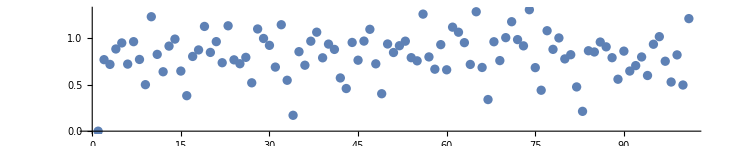

```mathematica
ListPlot[ColorDistance[Black,#]&/@%845,AspectRatio->1/5]
```

```mathematica
init={0,0,0};
n=20;
Function[{i,j,k},RGBColor/@(init+(#-Floor[#]&/@({ph3^-i,ph3^-j,ph3^-k}#))&/@Range[0,n])]@@@(Permutations@Range@3)//MatrixForm
```

(RGBColor[{0., 0., 0.}] | RGBColor[{0.8191725133961644, 0.671043606703789, 0.5497004779019701}] | RGBColor[{0.6383450267923287, 0.3420872134075781, 0.09940095580394015}] | RGBColor[{0.4575175401884932, 0.013130820111367125, 0.6491014337059102}] | RGBColor[{0.2766900535846575, 0.6841744268151562, 0.1988019116078803}] | RGBColor[{0.09586256698082174, 0.3552180335189452, 0.7485023895098504}] | RGBColor[{0.9150350803769864, 0.02626164022273425, 0.29820286741182045}] | RGBColor[{0.7342075937731503, 0.6973052469265237, 0.8479033453137905}] | RGBColor[{0.553380107169315, 0.36834885363031233, 0.3976038232157606}] | RGBColor[{0.37255262056547966, 0.03939246033410093, 0.9473043011177307}] | RGBColor[{0.19172513396164348, 0.7104360670378904, 0.49700477901970075}] | RGBColor[{0.010897647357808182, 0.3814796737416799, 0.046705256921670824}] | RGBColor[{0.8300701607539729, 0.0525232804454685, 0.5964057348236409}] | RGBColor[{0.6492426741501376, 0.7235668871492571, 0.14610621272561097}] | RGBColor[{0.4684151875463005, 0.3946104938530475, 0.695806690627581}] | RGBColor[{0.2875877009424652, 0.06565410055683607, 0.24550716852955112}] | RGBColor[{0.10676021433862992, 0.7366977072606247, 0.7952076464315212}] | RGBColor[{0.9259327277347946, 0.40774131396441327, 0.3449081243334913}] | RGBColor[{0.7451052411309593, 0.07878492066820186, 0.8946086022354613}] | RGBColor[{0.5642777545271223, 0.7498285273719922, 0.4443090801374314}] | RGBColor[{0.38345026792328696, 0.42087213407578083, 0.9940095580394015}]
RGBColor[{0., 0., 0.}] | RGBColor[{0.8191725133961644, 0.5497004779019701, 0.671043606703789}] | RGBColor[{0.6383450267923287, 0.09940095580394015, 0.3420872134075781}] | RGBColor[{0.4575175401884932, 0.6491014337059102, 0.013130820111367125}] | RGBColor[{0.2766900535846575, 0.1988019116078803, 0.6841744268151562}] | RGBColor[{0.09586256698082174, 0.7485023895098504, 0.3552180335189452}] | RGBColor[{0.9150350803769864, 0.29820286741182045, 0.02626164022273425}] | RGBColor[{0.7342075937731503, 0.8479033453137905, 0.6973052469265237}] | RGBColor[{0.553380107169315, 0.3976038232157606, 0.36834885363031233}] | RGBColor[{0.37255262056547966, 0.9473043011177307, 0.03939246033410093}] | RGBColor[{0.19172513396164348, 0.49700477901970075, 0.7104360670378904}] | RGBColor[{0.010897647357808182, 0.046705256921670824, 0.3814796737416799}] | RGBColor[{0.8300701607539729, 0.5964057348236409, 0.0525232804454685}] | RGBColor[{0.6492426741501376, 0.14610621272561097, 0.7235668871492571}] | RGBColor[{0.4684151875463005, 0.695806690627581, 0.3946104938530475}] | RGBColor[{0.2875877009424652, 0.24550716852955112, 0.06565410055683607}] | RGBColor[{0.10676021433862992, 0.7952076464315212, 0.7366977072606247}] | RGBColor[{0.9259327277347946, 0.3449081243334913, 0.40774131396441327}] | RGBColor[{0.7451052411309593, 0.8946086022354613, 0.07878492066820186}] | RGBColor[{0.5642777545271223, 0.4443090801374314, 0.7498285273719922}] | RGBColor[{0.38345026792328696, 0.9940095580394015, 0.42087213407578083}]
RGBColor[{0., 0., 0.}] | RGBColor[{0.671043606703789, 0.8191725133961644, 0.5497004779019701}] | RGBColor[{0.3420872134075781, 0.6383450267923287, 0.09940095580394015}] | RGBColor[{0.013130820111367125, 0.4575175401884932, 0.6491014337059102}] | RGBColor[{0.6841744268151562, 0.2766900535846575, 0.1988019116078803}] | RGBColor[{0.3552180335189452, 0.09586256698082174, 0.7485023895098504}] | RGBColor[{0.02626164022273425, 0.9150350803769864, 0.29820286741182045}] | RGBColor[{0.6973052469265237, 0.7342075937731503, 0.8479033453137905}] | RGBColor[{0.36834885363031233, 0.553380107169315, 0.3976038232157606}] | RGBColor[{0.03939246033410093, 0.37255262056547966, 0.9473043011177307}] | RGBColor[{0.7104360670378904, 0.19172513396164348, 0.49700477901970075}] | RGBColor[{0.3814796737416799, 0.010897647357808182, 0.046705256921670824}] | RGBColor[{0.0525232804454685, 0.8300701607539729, 0.5964057348236409}] | RGBColor[{0.7235668871492571, 0.6492426741501376, 0.14610621272561097}] | RGBColor[{0.3946104938530475, 0.4684151875463005, 0.695806690627581}] | RGBColor[{0.06565410055683607, 0.2875877009424652, 0.24550716852955112}] | RGBColor[{0.7366977072606247, 0.10676021433862992, 0.7952076464315212}] | RGBColor[{0.40774131396441327, 0.9259327277347946, 0.3449081243334913}] | RGBColor[{0.07878492066820186, 0.7451052411309593, 0.8946086022354613}] | RGBColor[{0.7498285273719922, 0.5642777545271223, 0.4443090801374314}] | RGBColor[{0.42087213407578083, 0.38345026792328696, 0.9940095580394015}]
RGBColor[{0., 0., 0.}] | RGBColor[{0.671043606703789, 0.5497004779019701, 0.8191725133961644}] | RGBColor[{0.3420872134075781, 0.09940095580394015, 0.6383450267923287}] | RGBColor[{0.013130820111367125, 0.6491014337059102, 0.4575175401884932}] | RGBColor[{0.6841744268151562, 0.1988019116078803, 0.2766900535846575}] | RGBColor[{0.3552180335189452, 0.7485023895098504, 0.09586256698082174}] | RGBColor[{0.02626164022273425, 0.29820286741182045, 0.9150350803769864}] | RGBColor[{0.6973052469265237, 0.8479033453137905, 0.7342075937731503}] | RGBColor[{0.36834885363031233, 0.3976038232157606, 0.553380107169315}] | RGBColor[{0.03939246033410093, 0.9473043011177307, 0.37255262056547966}] | RGBColor[{0.7104360670378904, 0.49700477901970075, 0.19172513396164348}] | RGBColor[{0.3814796737416799, 0.046705256921670824, 0.010897647357808182}] | RGBColor[{0.0525232804454685, 0.5964057348236409, 0.8300701607539729}] | RGBColor[{0.7235668871492571, 0.14610621272561097, 0.6492426741501376}] | RGBColor[{0.3946104938530475, 0.695806690627581, 0.4684151875463005}] | RGBColor[{0.06565410055683607, 0.24550716852955112, 0.2875877009424652}] | RGBColor[{0.7366977072606247, 0.7952076464315212, 0.10676021433862992}] | RGBColor[{0.40774131396441327, 0.3449081243334913, 0.9259327277347946}] | RGBColor[{0.07878492066820186, 0.8946086022354613, 0.7451052411309593}] | RGBColor[{0.7498285273719922, 0.4443090801374314, 0.5642777545271223}] | RGBColor[{0.42087213407578083, 0.9940095580394015, 0.38345026792328696}]
RGBColor[{0., 0., 0.}] | RGBColor[{0.5497004779019701, 0.8191725133961644, 0.671043606703789}] | RGBColor[{0.09940095580394015, 0.6383450267923287, 0.3420872134075781}] | RGBColor[{0.6491014337059102, 0.4575175401884932, 0.013130820111367125}] | RGBColor[{0.1988019116078803, 0.2766900535846575, 0.6841744268151562}] | RGBColor[{0.7485023895098504, 0.09586256698082174, 0.3552180335189452}] | RGBColor[{0.29820286741182045, 0.9150350803769864, 0.02626164022273425}] | RGBColor[{0.8479033453137905, 0.7342075937731503, 0.6973052469265237}] | RGBColor[{0.3976038232157606, 0.553380107169315, 0.36834885363031233}] | RGBColor[{0.9473043011177307, 0.37255262056547966, 0.03939246033410093}] | RGBColor[{0.49700477901970075, 0.19172513396164348, 0.7104360670378904}] | RGBColor[{0.046705256921670824, 0.010897647357808182, 0.3814796737416799}] | RGBColor[{0.5964057348236409, 0.8300701607539729, 0.0525232804454685}] | RGBColor[{0.14610621272561097, 0.6492426741501376, 0.7235668871492571}] | RGBColor[{0.695806690627581, 0.4684151875463005, 0.3946104938530475}] | RGBColor[{0.24550716852955112, 0.2875877009424652, 0.06565410055683607}] | RGBColor[{0.7952076464315212, 0.10676021433862992, 0.7366977072606247}] | RGBColor[{0.3449081243334913, 0.9259327277347946, 0.40774131396441327}] | RGBColor[{0.8946086022354613, 0.7451052411309593, 0.07878492066820186}] | RGBColor[{0.4443090801374314, 0.5642777545271223, 0.7498285273719922}] | RGBColor[{0.9940095580394015, 0.38345026792328696, 0.42087213407578083}]
RGBColor[{0., 0., 0.}] | RGBColor[{0.5497004779019701, 0.671043606703789, 0.8191725133961644}] | RGBColor[{0.09940095580394015, 0.3420872134075781, 0.6383450267923287}] | RGBColor[{0.6491014337059102, 0.013130820111367125, 0.4575175401884932}] | RGBColor[{0.1988019116078803, 0.6841744268151562, 0.2766900535846575}] | RGBColor[{0.7485023895098504, 0.3552180335189452, 0.09586256698082174}] | RGBColor[{0.29820286741182045, 0.02626164022273425, 0.9150350803769864}] | RGBColor[{0.8479033453137905, 0.6973052469265237, 0.7342075937731503}] | RGBColor[{0.3976038232157606, 0.36834885363031233, 0.553380107169315}] | RGBColor[{0.9473043011177307, 0.03939246033410093, 0.37255262056547966}] | RGBColor[{0.49700477901970075, 0.7104360670378904, 0.19172513396164348}] | RGBColor[{0.046705256921670824, 0.3814796737416799, 0.010897647357808182}] | RGBColor[{0.5964057348236409, 0.0525232804454685, 0.8300701607539729}] | RGBColor[{0.14610621272561097, 0.7235668871492571, 0.6492426741501376}] | RGBColor[{0.695806690627581, 0.3946104938530475, 0.4684151875463005}] | RGBColor[{0.24550716852955112, 0.06565410055683607, 0.2875877009424652}] | RGBColor[{0.7952076464315212, 0.7366977072606247, 0.10676021433862992}] | RGBColor[{0.3449081243334913, 0.40774131396441327, 0.9259327277347946}] | RGBColor[{0.8946086022354613, 0.07878492066820186, 0.7451052411309593}] | RGBColor[{0.4443090801374314, 0.7498285273719922, 0.5642777545271223}] | RGBColor[{0.9940095580394015, 0.42087213407578083, 0.38345026792328696}])

```mathematica
?Function
```

Function[body] or body& is a pure (or "anonymous") function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters. 
Function[params,body,attrs] is a pure function that is treated as having attributes attrs for purposes of evaluation.